## Spectral Decomposition

### Definitions

```mathematica
Clear[σ,ϕ,α,β,A2]
```

```mathematica
σSol = {σ->(3+Sqrt[5])/2};
```

```mathematica
σ/.σSol//N
1/σ/.σSol//N
1/σ^2/.σSol//N
```

2.61803

0.381966

0.145898

```mathematica
ϕDef={ϕ -> σ-1};
```

```mathematica
ϕ/.ϕDef/.σSol//Simplify
%//N
1/%
%^2
```

1/2 (1+√5)

1.61803

0.618034

0.381966

```mathematica
ϕSol={ϕ -> (1+Sqrt[5])/2};
```

```mathematica
αDef={α->1/Sqrt[Simplify[1+ϕ^2]]};
βDef={β->ϕ/Sqrt[Simplify[1+ϕ^2]]};
αβDef={α->1/Sqrt[Simplify[1+ϕ^2]],β->ϕ/Sqrt[Simplify[1+ϕ^2]]};
A2Def={A2->α+β };
```

```mathematica
α/.αDef/.ϕDef/.σSol//Simplify
%//N
%^2
```

√(2/(5+√5))

0.525731

0.276393

```mathematica
β/.βDef/.ϕDef/.σSol//Simplify
%//N
%^2
```

(1+√5)/(√(2 (5+√5)))

0.850651

0.723607

```mathematica
A2/.A2Def/.αDef/.βDef/.ϕDef/.σSol//Simplify
%//N
1/%
%^2
```

(3+√5)/(√(2 (5+√5)))

1.37638

0.726543

0.527864

```mathematica
αSol={α->Sqrt[2/(5+Sqrt[5])]};
βSol={β->(1+Sqrt[5])/Sqrt[2(5+Sqrt[5])]};
αβSol=Join[αSol,βSol];
A2Sol={A2-> (3+Sqrt[5])/Sqrt[2(5+Sqrt[5])]};
varSol=Join[αβSol,A2Sol,σSol,ϕSol];
```

### The space of step functions (Ulam method).

#### Considerations

The effect of the Perron-Frobenius operator is to smooth the dependency of a distribution along the unstable manifold. The decaying modes should be found by restricting the operator on functions of u only.

Here are the inverse of the u-map and the u-map. The inverse has three branches because the u-map is not invertible.

```mathematica
invFu[u_]:=Piecewise[{
{{u/σ,u/σ+α,999999999},0≤ u<α},
{{u/σ,u/σ+α,u/σ+β},α≤u<A2}
}]
invFu[u]/.varSol//N
Fu[u_]:=Piecewise[{
{σ u,0≤ u<α},
{σ u-A2,α≤ u<2α},
{σ u-A2-β,2α≤ u<A2}
}]
Fu[u]/.varSol//N
```

{0.524992,1.05072,1.37564}

1.37132

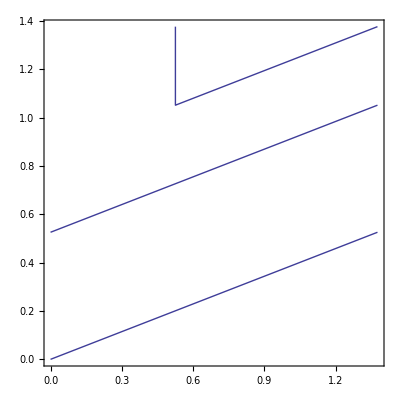

```mathematica
Plot[invFu[u]/.varSol//N, {u,0,A2/.A2Sol//N},PlotRange->{{0,A2/.A2Sol//N},{0,A2/.A2Sol//N}},Frame->True, ImageSize->Scaled[0.5], AspectRatio-> Automatic]
```

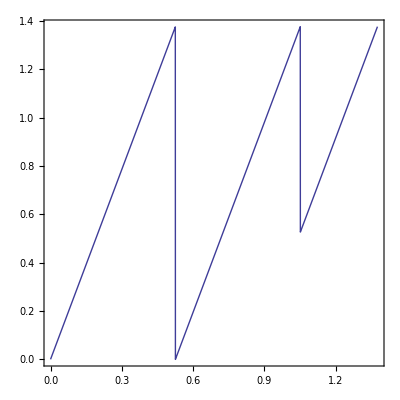

```mathematica
Plot[Fu[u]/.varSol//N, {u,0,A2/.A2Sol//N},PlotRange->{{0,A2/.A2Sol//N},{0,A2/.A2Sol//N}},Frame->True, ImageSize->Scaled[0.5], AspectRatio-> Automatic]
```

These are the Perron-Frobenius operator and the Koopman operator of the u-map.

```mathematica
Subscript[ℒ, 1D][ρ_,u_]:= Piecewise[{
{(ρ[u/σ]+ρ[u/σ+α])/σ,0≤ u<α},
{(ρ[u/σ]+ρ[u/σ+α]+ρ[u/σ+β])/σ,α≤u<A2}
}]
Subscript[𝒦, 1D][ρ_,u_]:= ρ[Fu[u]]
```

```mathematica
LPlot[f_]:=Plot[Subscript[ℒ, 1D][f,u]/.varSol//N, {u,0,A2/.A2Sol//N},PlotRange->{{0,A2/.A2Sol//N},{-1,1}},Frame->True, ImageSize->Scaled[0.75], AspectRatio-> 0.5]
```

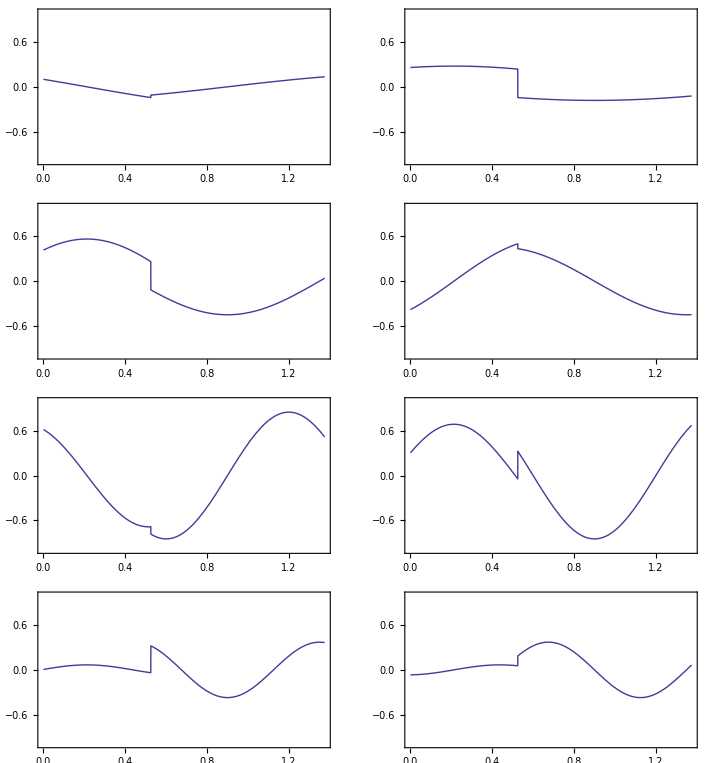

```mathematica
plotR11=LPlot[Cos[2 Pi#/A2/.A2Sol//N]&];plotI11=LPlot[Sin[2 Pi#/A2/.A2Sol//N]&];plotR21=LPlot[Cos[4 Pi#/A2/.A2Sol//N]&];plotI21=LPlot[Sin[4 Pi#/A2/.A2Sol//N]&];plotR31=LPlot[Cos[6 Pi#/A2/.A2Sol//N]&];plotI31=LPlot[Sin[6 Pi#/A2/.A2Sol//N]&];plotR41=LPlot[Cos[8 Pi#/A2/.A2Sol//N]&];plotI41=LPlot[Sin[8 Pi#/A2/.A2Sol//N]&];GraphicsGrid[{{plotR11,plotI11},{plotR21,plotI21},{plotR31,plotI31},{plotR41,plotI41}}]
```

The Perron-Frobenius operator creates a discontinuity at u = α and decreases the frequency of the harmonic.

```mathematica
KPlot[f_]:=Plot[Subscript[𝒦, 1D][f,u]/.varSol//N, {u,0,A2/.A2Sol//N},PlotRange->{{0,A2}/.A2Sol//N,{-1,1}},Frame->True, ImageSize->Scaled[0.75], AspectRatio-> 0.5]/.A2Sol
```

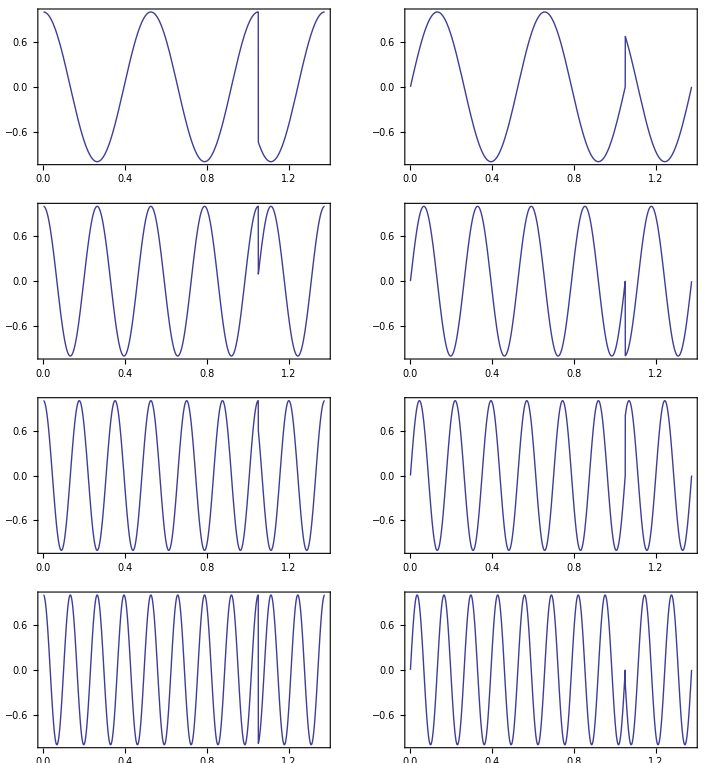

```mathematica
plotR11=KPlot[Cos[2 Pi#/A2/.A2Sol//N]&];plotI11=KPlot[Sin[2 Pi#/A2/.A2Sol//N]&];plotR21=KPlot[Cos[4 Pi#/A2/.A2Sol//N]&];plotI21=KPlot[Sin[4 Pi#/A2/.A2Sol//N]&];plotR31=KPlot[Cos[6 Pi#/A2/.A2Sol//N]&];plotI31=KPlot[Sin[6 Pi#/A2/.A2Sol//N]&];plotR41=KPlot[Cos[8 Pi#/A2/.A2Sol//N]&];plotI41=KPlot[Sin[8 Pi#/A2/.A2Sol//N]&];GraphicsGrid[{{plotR11,plotI11},{plotR21,plotI21},{plotR31,plotI31},{plotR41,plotI41}}]
```

The Koopman operator creates a discontinuity at u = 2α and increases the frequency of the harmonic.

#### The period 1 partition

```mathematica
SPlot[f_]:=Plot[f, {u,0,A2/.A2Sol//N},PlotRange->{{0,A2/.A2Sol//N},{0,1.1Max[a]}},Frame->True, ImageSize->Scaled[0.75], AspectRatio-> Automatic]
```

Let's define the partition 𝔓_1 = {[0,α[,[α,α+β[} and consider the space of step functions with step at α: 𝕊𝔓_1.

{0.0847331,1.1232}

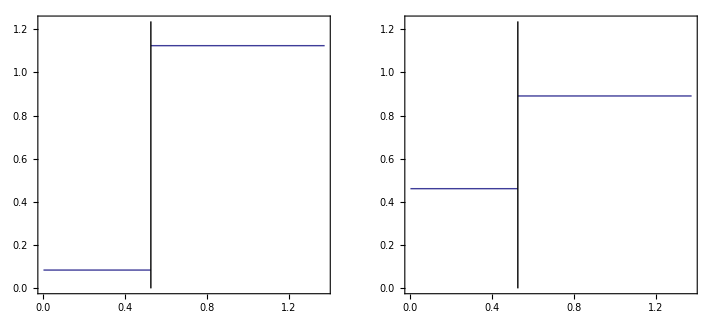

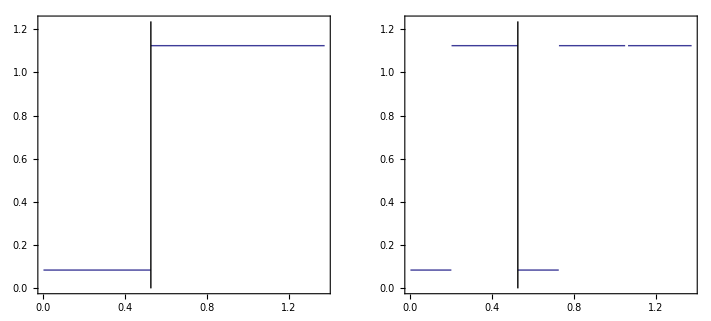

```mathematica
Clear[Step2]
Step2[a_,u_]:=(a [[1]]HeavisideTheta[u]HeavisideTheta[α-u]+a[[2]] HeavisideTheta[u-α]HeavisideTheta[A2-u+α])/.varSol//N;

Clear[a]
a={RandomReal[1],RandomReal[1]};
a=a/(a[[1]] α+a[[2]] β)/.αβSol//N
post = Graphics[Line[{{α,0},{α,1.1 Max[a]}}]]/.αβSol//N;

plotS1=SPlot[Step2[a,u]];plotLS1=SPlot[Subscript[ℒ, 1D][Step2[a,#//N]&,u]/.varSol//N];GraphicsGrid[{{Show[plotS1,post],Show[plotLS1,post]}}]
plotKS1=SPlot[Subscript[𝒦, 1D][Step2[a,#//N]&,u]/.varSol//N];GraphicsGrid[{{Show[plotS1,post],Show[plotKS1,post]}}]
```

The Perron-Frobenius operator sends an element of 𝕊𝔓_1 to another element of 𝕊𝔓_1. However Koopman introduces two additional steps besides the one at α. The image of 𝕊𝔓_1 under Koopman is not in 𝕊𝔓_1.

#### n=5 bad partition

```mathematica
index[grid_,x_]:=
Module[{ind=Length[grid]},
Do[If[grid[[i]]≤ x<grid[[i+1]],ind=i],{i,Length[grid]-1}];
ind
]
```

```mathematica
mapStepFunctionAndPlotResult[]:=Module[
{StepFunction={},
LStepFunction = {},
KStepFunction = {},
KLStepFunction={}
},
Do[ 
StepFunction= Join[StepFunction,Table[{(gridPoint[[j+1]]-gridPoint[[j]])(i-1)/n+gridPoint[[j]],a[[j]]},{i,n}]//N],
{j,Length[a]}];
Block[
{grid=Transpose[StepFunction][[1]]},
Do[
u=grid[[i]];
u1=(u/σ)/.varSol//N;
u2=(u/σ+α)/.varSol//N;
u3=(u/σ+β)/.varSol//N;
value1=StepFunction[[index[grid,u1]]][[2]];
value2=StepFunction[[index[grid,u2]]][[2]];
value3=StepFunction[[index[grid,u3]]][[2]];
value=Piecewise[{
{(value1+value2)/σ,0≤ u<α}/.varSol//N,
{(value1+value2+value3)/σ,α≤u<A2}/.varSol//N
}];
(*Print[{u,value1,value2,value3,value}];*)
LStepFunction=Append[LStepFunction,{u,value}];
u1=(σ u)/.varSol//N;
u2=(σ u-A2)/.varSol//N;
u3=(σ u-A2-β)/.varSol//N;
value=Piecewise[{
{StepFunction[[index[grid,u1]]][[2]],0≤ u<α}/.varSol//N,
{StepFunction[[index[grid,u2]]][[2]],α≤u<2α}/.varSol//N,
{StepFunction[[index[grid,u3]]][[2]],2α≤u<A2}/.varSol//N
}];
KStepFunction=Append[KStepFunction,{u,value}],
{i,Length[StepFunction]}];
Do[
u=grid[[i]];
u1=(σ u)/.varSol//N;
u2=(σ u-A2)/.varSol//N;
u3=(σ u-A2-β)/.varSol//N;
value=Piecewise[{
{LStepFunction[[index[grid,u1]]][[2]],0≤ u<α}/.varSol//N,
{LStepFunction[[index[grid,u2]]][[2]],α≤u<2α}/.varSol//N,
{LStepFunction[[index[grid,u3]]][[2]],2α≤u<A2}/.varSol//N
}];
KLStepFunction=Append[KLStepFunction,{u,value}],
{i,Length[LStepFunction]}]
];
{ListPlot[StepFunction, PlotRange->{{0,A2/.A2Sol//N},{0,1.1 Max[a]}},Frame->True, ImageSize->Scaled[scale], AspectRatio-> 0.5,Joined->True],
ListPlot[LStepFunction, PlotRange->{{0,A2/.A2Sol//N},{0,1.1 Max[a]}},Frame->True, ImageSize->Scaled[scale], AspectRatio-> 0.5,Joined->True],
ListPlot[KStepFunction, PlotRange->{{0,A2/.A2Sol//N},{0,1.1 Max[a]}},Frame->True, ImageSize->Scaled[scale], AspectRatio-> 0.5,Joined->True],
ListPlot[KLStepFunction, PlotRange->{{0,A2/.A2Sol//N},{0,1.1 Max[a]}},Frame->True, ImageSize->Scaled[scale], AspectRatio-> 0.5,Joined->True]}
]
scale=1;
```

Let's define the partition 𝔓_4 = {[0,α/2[,[α/2,α[,[α,3α/2[,[3α/2,2α[,[2α,α+β[} and consider the space of step functions with a step at each border point of this partition: 𝕊𝔓_4.

```mathematica
gridPoint = {0,α/2,α,3α/2,2α,α+β}/.varSol//N
Fu/@gridPoint/.varSol//N
invFu/@gridPoint/.varSol//N
```

{0.,0.262866,0.525731,0.788597,1.05146,1.37638}

{0.,0.688191,0.,0.688191,0.525731,0.}

{{0.,0.525731,1.×10^9},{0.100406,0.626137,1.×10^9},{0.200811,0.726543,1.05146},{0.301217,0.826948,1.15187},{0.401623,0.927354,1.25227},0.}

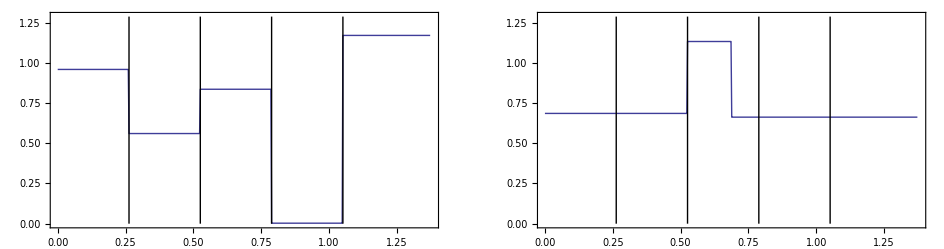

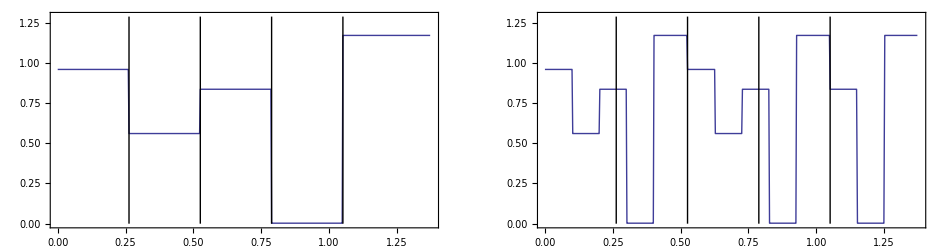

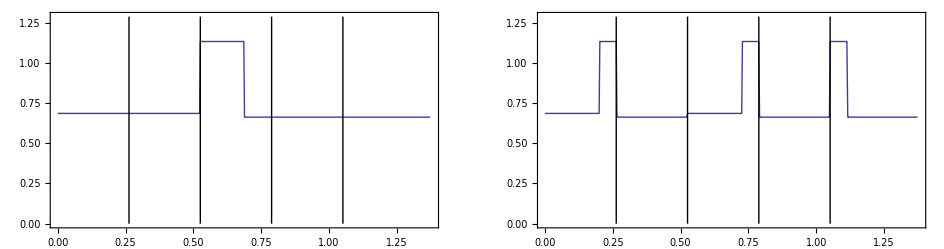

```mathematica
gridPoint = {0,α/2,α,3α/2,2α,α+β}/.varSol//N;
n=100;
a=Table[RandomReal[1],{5}];
a=a/Sum[a[[i]](gridPoint[[i+1]]-gridPoint[[i]]),{i,5}];
fence=Table[Graphics[Line[{{gridPoint[[i]],0},{gridPoint[[i]],1.1 Max[a]}}]],{i,2,Length[a]}];
{plotOfS,plotOfLS,plotOfKS,plotOfKLS}=mapStepFunctionAndPlotResult[];
GraphicsGrid[{{Show[plotOfS,fence],Show[plotOfLS,fence]}}]
GraphicsGrid[{{Show[plotOfS,fence],Show[plotOfKS,fence]}}]
GraphicsGrid[{{Show[plotOfLS,fence],Show[plotOfKLS,fence]}}]
```

The Perron-Frobenius operator removes three steps, preserves the step at α and adds a new step between α and 3α/2 at Fu(α/2)=Fu(3α/2).

Koopman preserves the steps at α and 2α, removes the other ones and adds new steps within the partition cells at the inverse images of the partition points under the u-map. In fact it simply squeezes the whole step function into [0,α[ and once again into [α,2α[ and the segment of the step function originally on [α,α+β[ into [2α,α+β[.

The images of 𝕊𝔓_4 under either operator is not in 𝕊𝔓_4.

#### n=10 bad partition

```mathematica
gridPoint = {0,α/4,α/2,3α/4,α,5α/4,3α/2,7α/4,2α,9α/4,α+β}/.varSol//N
Fu/@gridPoint/.varSol//N
invFu/@gridPoint/.varSol//N
```

{0.,0.131433,0.262866,0.394298,0.525731,0.657164,0.788597,0.920029,1.05146,1.1829,1.37638}

{0.,0.344095,0.688191,1.03229,0.,0.344095,0.688191,1.03229,0.525731,0.869827,0.}

{{0.,0.525731,1.×10^9},{0.0502029,0.575934,1.×10^9},{0.100406,0.626137,1.×10^9},{0.150609,0.67634,1.×10^9},{0.200811,0.726543,1.05146},{0.251014,0.776745,1.10167},{0.301217,0.826948,1.15187},{0.35142,0.877151,1.20207},{0.401623,0.927354,1.25227},{0.451826,0.977557,1.30248},0.}

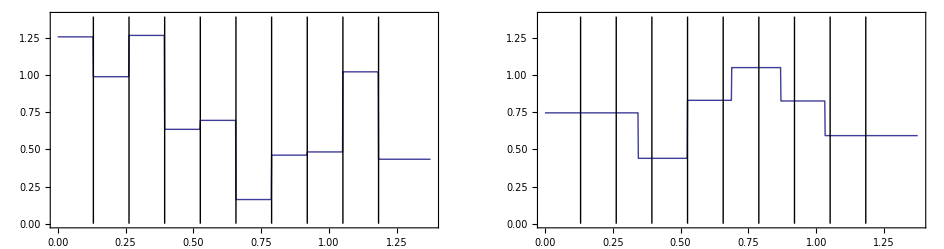

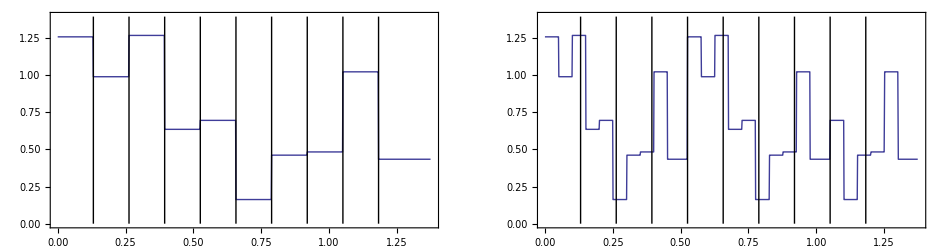

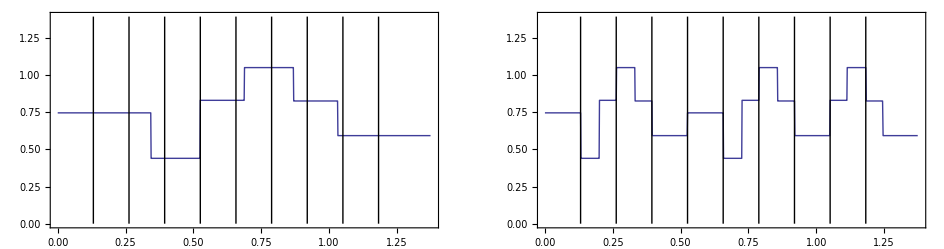

```mathematica
gridPoint = {0,α/4,α/2,3α/4,α,5α/4,3α/2,7α/4,2α,9α/4,α+β}/.varSol//N;
n=100;
a=Table[RandomReal[1],{10}];
a=a/Sum[a[[i]](gridPoint[[i+1]]-gridPoint[[i]]),{i,10}];
fence=Table[Graphics[Line[{{gridPoint[[i]],0},{gridPoint[[i]],1.1 Max[a]}}]],{i,2,Length[a]}];
{plotOfS,plotOfLS,plotOfKS,plotOfKLS}=mapStepFunctionAndPlotResult[];
GraphicsGrid[{{Show[plotOfS,fence],Show[plotOfLS,fence]}}]
GraphicsGrid[{{Show[plotOfS,fence],Show[plotOfKS,fence]}}]
GraphicsGrid[{{Show[plotOfLS,fence],Show[plotOfKLS,fence]}}]
```

#### Period 2 periodic point n=19 partition - Operator construction

The new steps created by the action of Perron-Frobenius are images of the partition points under the u-map. The new steps introduced by Koopman are inverse images of the partition points. We should expect no new steps to be created if the partition points are periodic points of the u map.

Let's start with the partition defined by the periodic points of period 2, 𝔓^2.

```mathematica
gridPoint={0,0.2351141009169892,0.5257311121191336,0.6155367074350505,0.8506508083520398,0.995959313953112,1.2310734148701015,1.3763819204711734}
Length[%]
```

{0,0.235114,0.525731,0.615537,0.850651,0.995959,1.23107,1.37638}

8

{0.262031,0.89561,0.314047,1.40717,1.08182,0.323148,0.59109}

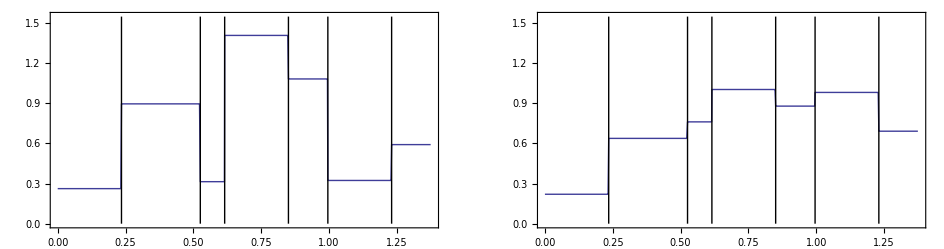

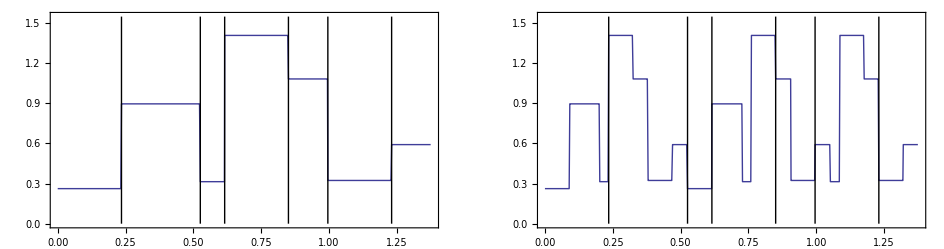

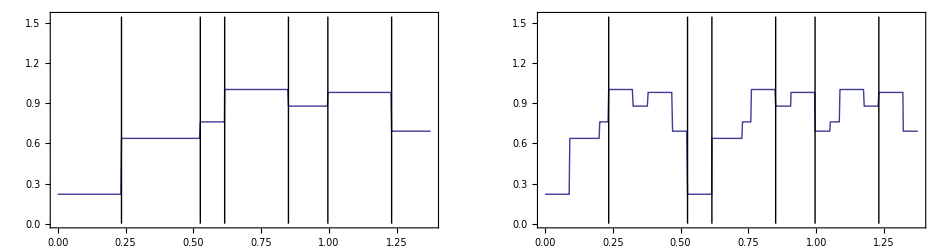

```mathematica
n=100;
a=Table[RandomReal[1],{Length[gridPoint]-1}];
a=a/Sum[a[[i]](gridPoint[[i+1]]-gridPoint[[i]]),{i,Length[a]}]//N
fence=Table[Graphics[Line[{{gridPoint[[i]],0},{gridPoint[[i]],1.1 Max[a]}}]],{i,2,Length[a]}];
scale=1;
{plotOfS,plotOfLS,plotOfKS,plotOfKLS}=mapStepFunctionAndPlotResult[];
GraphicsGrid[{{Show[plotOfS,fence],Show[plotOfLS,fence]}}]
GraphicsGrid[{{Show[plotOfS,fence],Show[plotOfKS,fence]}}]
GraphicsGrid[{{Show[plotOfLS,fence],Show[plotOfKLS,fence]}}]
```

Indeed Perron-Frobenius maps an element of 𝕊𝔓^2 to another element of 𝕊𝔓^2. However, Koopman does not because each periodic point has up to three inverse images since the u-map is not invertible.

We create a finer partition by adding to the points defining 𝔓^2 all their inverse images. We call this partition 𝔓^(*2).

```mathematica
gridPeriodicPoint=gridPoint
Length[%]
gridPoint={0.,0.08980559531591706,0.20081141588622728,0.2351141009169892,0.3249196962329063,0.38042260651806137,0.47022820183397857,0.5257311121191336,0.6155367074350505,0.7265425280053608,0.7608452130361227,0.8506508083520398,0.9061537186371948,0.940456403667957,0.995959313953112,1.0514622242382672,1.0857649092690291,1.1755705045849463,1.2310734148701015,1.3208790101860186,1.3763819204711734}
Length[%]
```

{0,0.235114,0.525731,0.615537,0.850651,0.995959,1.23107,1.37638}

8

{0.,0.0898056,0.200811,0.235114,0.32492,0.380423,0.470228,0.525731,0.615537,0.726543,0.760845,0.850651,0.906154,0.940456,0.995959,1.05146,1.08576,1.17557,1.23107,1.32088,1.37638}

21

{1.32383,1.3034,1.11302,0.815489,0.989597,0.696016,1.1739,0.266251,0.266093,1.2085,0.487543,0.464367,0.475234,0.664189,0.316998,0.465183,0.563646,0.696448,0.620536,0.833223}

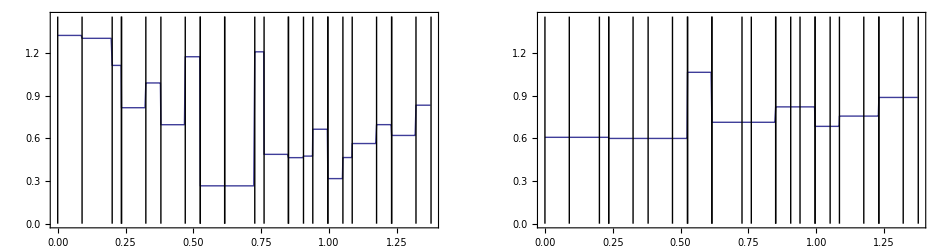

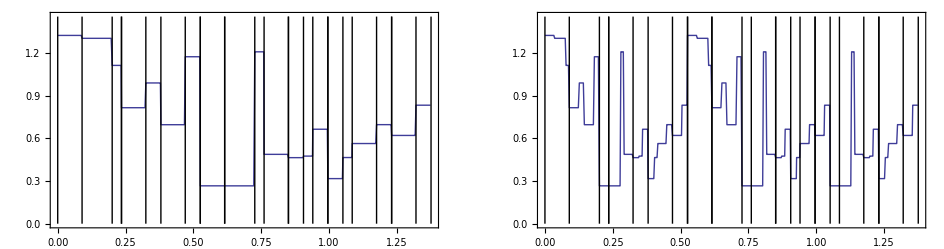

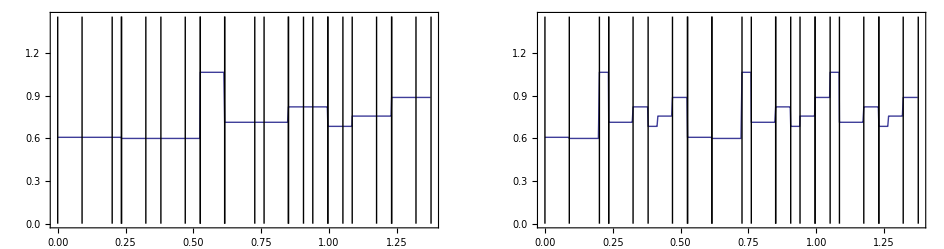

```mathematica
n=30;
a=Table[RandomReal[1],{Length[gridPoint]-1}];
a=a/Sum[a[[i]](gridPoint[[i+1]]-gridPoint[[i]]),{i,Length[a]}]//N
fence=Table[Graphics[Line[{{gridPoint[[i]],0},{gridPoint[[i]],1.1 Max[a]}}]],{i,2,Length[a]}];
fence2=Table[Graphics[{Thick,Line[{{gridPeriodicPoint[[i]],0},{gridPeriodicPoint[[i]],1.1 Max[a]}}]}],{i,Length[gridPeriodicPoint]}];
{plotOfS,plotOfLS,plotOfKS,plotOfKLS}=mapStepFunctionAndPlotResult[];
GraphicsGrid[{{Show[plotOfS,fence,fence2],Show[plotOfLS,fence,fence2]}}]
GraphicsGrid[{{Show[plotOfS,fence,fence2],Show[plotOfKS,fence,fence2]}}]
GraphicsGrid[{{Show[plotOfLS,fence,fence2],Show[plotOfKLS,fence,fence2]}}]
```

Perron-Frobenius maps an element of 𝕊𝔓^(*2) to another element of  𝕊𝔓^(*2) with less steps. We would have liked it to be an element of 𝕊𝔓^2⊂ 𝕊𝔓^(*2) but it is not because it has one step too many. We would like to see something like ℒ (𝕊𝔓^(*2)) ⊂ 𝕊𝔓^2 and 𝒦(ℒ (𝕊𝔓^(*2))) ⊂ 𝕊𝔓^(*2). But we are not quite there yet.

The easiest way to see where the extra step is coming from is to create the matrix representation of Perron-Frobenius and look at it. The first two branches of the map represented in the matrix should be identical but they are not. The second one has one kink too many.

```mathematica
cellFind[{u1_,u2_}]:=
Module[{i=1,c=0},
While[u2> cellList[[i,2]],c=i;i++];
c
]
```

```mathematica
cellList=Transpose[{Table[i-1,{i,Length[gridPoint]}],gridPoint}]
L=Table[0,{Length[gridPoint]-1},{Length[gridPoint]-1}];
Do[
Print[i];
interval={gridPoint[[i]]/σ,gridPoint[[i+1]]/σ}/.varSol//N;
cell=cellFind[interval];
Print[interval,"->",cell];
L[[i,cell]]=1;
interval={gridPoint[[i]]/σ+α,gridPoint[[i+1]]/σ+α}/.varSol//N;
cell=cellFind[interval];
Print[interval,"->",cell];
L[[i,cell]]=1;
If[gridPoint[[i]]≥ α/.varSol//N,
interval={gridPoint[[i]]/σ+β,gridPoint[[i+1]]/σ+β}/.varSol//N;
cell=cellFind[interval];
Print[interval,"->",cell]];
  L[[i,cell]]=1,
{i,Length[gridPoint]-1}]
ArrayPlot[L,Mesh->True]
```

{{0,0.},{1,0.0898056},{2,0.200811},{3,0.235114},{4,0.32492},{5,0.380423},{6,0.470228},{7,0.525731},{8,0.615537},{9,0.726543},{10,0.760845},{11,0.850651},{12,0.906154},{13,0.940456},{14,0.995959},{15,1.05146},{16,1.08576},{17,1.17557},{18,1.23107},{19,1.32088},{20,1.37638}}

1

{0.,0.0343027}->1

{0.525731,0.560034}->8

2

{0.0343027,0.0767031}->1

{0.560034,0.602434}->8

3

{0.0767031,0.0898056}->1

{0.602434,0.615537}->8

4

{0.0898056,0.124108}->2

{0.615537,0.649839}->9

5

{0.124108,0.145309}->2

{0.649839,0.67104}->9

6

{0.145309,0.179611}->2

{0.67104,0.705342}->9

7

{0.179611,0.200811}->2

{0.705342,0.726543}->9

8

{0.200811,0.235114}->3

{0.726543,0.760845}->10

{1.05146,1.08576}->16

9

{0.235114,0.277515}->4

{0.760845,0.803246}->11

{1.08576,1.12817}->17

10

{0.277515,0.290617}->4

{0.803246,0.816348}->11

{1.12817,1.14127}->17

11

{0.290617,0.32492}->4

{0.816348,0.850651}->11

{1.14127,1.17557}->17

12

{0.32492,0.34612}->5

{0.850651,0.871851}->12

{1.17557,1.19677}->18

13

{0.34612,0.359222}->5

{0.871851,0.884953}->12

{1.19677,1.20987}->18

14

{0.359222,0.380423}->5

{0.884953,0.906154}->12

{1.20987,1.23107}->18

15

{0.380423,0.401623}->6

{0.906154,0.927354}->13

{1.23107,1.25227}->19

16

{0.401623,0.414725}->6

{0.927354,0.940456}->13

{1.25227,1.26538}->19

17

{0.414725,0.449028}->6

{0.940456,0.974759}->14

{1.26538,1.29968}->19

18

{0.449028,0.470228}->6

{0.974759,0.995959}->14

{1.29968,1.32088}->19

19

{0.470228,0.504531}->7

{0.995959,1.03026}->15

{1.32088,1.35518}->20

20

{0.504531,0.525731}->7

{1.03026,1.05146}->15

{1.35518,1.37638}->20

-Graphics-

We just need to prune one inverse image from the points defining 𝕊𝔓^(*2). The result is precisely what we want, namely ℒ (𝕊𝔓^(*2)) ⊂ 𝕊(𝔓^2) and 𝒦(ℒ (𝕊𝔓^(*2))) ⊂ 𝕊𝔓^(*2).

```mathematica
gridPoint={0.,0.08980559531591706,0.20081141588622728,0.2351141009169892,0.3249196962329063,0.38042260651806137,0.47022820183397857,0.5257311121191336,0.6155367074350505,0.7265425280053608,0.7608452130361227,0.8506508083520398,0.9061537186371948,(*0.940456403667957,*)0.995959313953112,1.0514622242382672,1.0857649092690291,1.1755705045849463,1.2310734148701015,1.3208790101860186,1.3763819204711734}
Length[%]
iAlpha=8;
```

{0.,0.0898056,0.200811,0.235114,0.32492,0.380423,0.470228,0.525731,0.615537,0.726543,0.760845,0.850651,0.906154,0.995959,1.05146,1.08576,1.17557,1.23107,1.32088,1.37638}

20

{0.615217,1.17065,0.453466,1.00797,0.353046,1.30401,0.875058,0.0356044,0.29453,0.829219,0.703683,0.363697,1.14225,0.29145,0.0481144,0.720395,0.788328,1.0727,0.910671}

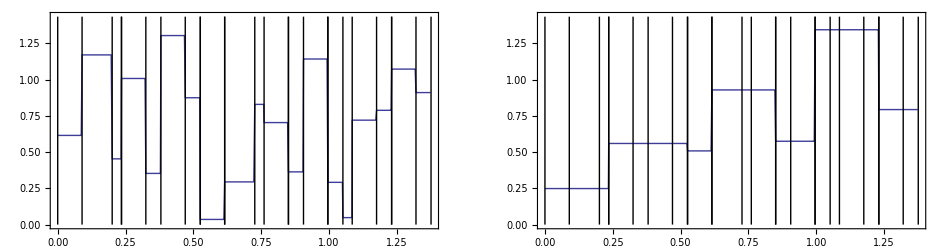

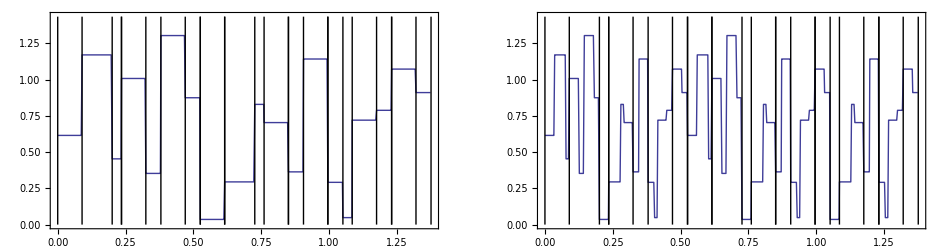

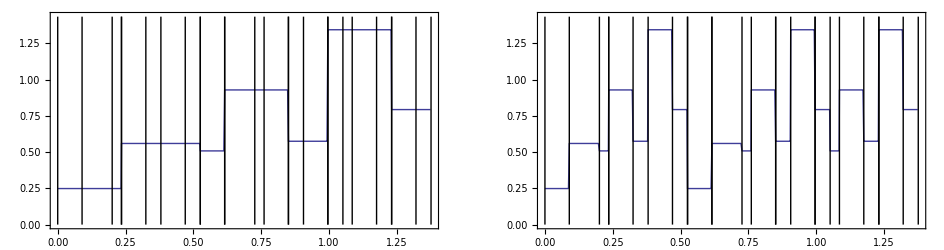

```mathematica
n=30;
a=Table[RandomReal[1],{Length[gridPoint]-1}];
a=a/Sum[a[[i]](gridPoint[[i+1]]-gridPoint[[i]]),{i,Length[a]}]//N
fence=Table[Graphics[Line[{{gridPoint[[i]],0},{gridPoint[[i]],1.1 Max[a]}}]],{i,2,Length[a]}];
fence2=Table[Graphics[{Thick,Line[{{gridPeriodicPoint[[i]],0},{gridPeriodicPoint[[i]],1.1 Max[a]}}]}],{i,Length[gridPeriodicPoint]}];
{plotOfS,plotOfLS,plotOfKS,plotOfKLS}=mapStepFunctionAndPlotResult[];
GraphicsGrid[{{Show[plotOfS,fence,fence2],Show[plotOfLS,fence,fence2]}}]
GraphicsGrid[{{Show[plotOfS,fence,fence2],Show[plotOfKS,fence,fence2]}}]
GraphicsGrid[{{Show[plotOfLS,fence,fence2],Show[plotOfKLS,fence,fence2]}}]
```

```mathematica
cellList=Transpose[{Table[i-1,{i,Length[gridPoint]}],gridPoint}]
L=Table[0,{Length[gridPoint]-1},{Length[gridPoint]-1}];
Do[
Print[i];
interval={gridPoint[[i]]/σ,gridPoint[[i+1]]/σ}/.varSol//N;
cell=cellFind[interval];
Print[interval,"->",cell];
L[[i,cell]]=1;
interval={gridPoint[[i]]/σ+α,gridPoint[[i+1]]/σ+α}/.varSol//N;
cell=cellFind[interval];
Print[interval,"->",cell];
L[[i,cell]]=1;
If[gridPoint[[i]]≥ α/.varSol//N,
interval={gridPoint[[i]]/σ+β,gridPoint[[i+1]]/σ+β}/.varSol//N;
cell=cellFind[interval];
Print[interval,"->",cell]];
  L[[i,cell]]=1,
{i,Length[gridPoint]-1}]
ArrayPlot[L,Mesh->True]
```

{{0,0.},{1,0.0898056},{2,0.200811},{3,0.235114},{4,0.32492},{5,0.380423},{6,0.470228},{7,0.525731},{8,0.615537},{9,0.726543},{10,0.760845},{11,0.850651},{12,0.906154},{13,0.995959},{14,1.05146},{15,1.08576},{16,1.17557},{17,1.23107},{18,1.32088},{19,1.37638}}

1

{0.,0.0343027}->1

{0.525731,0.560034}->8

2

{0.0343027,0.0767031}->1

{0.560034,0.602434}->8

3

{0.0767031,0.0898056}->1

{0.602434,0.615537}->8

4

{0.0898056,0.124108}->2

{0.615537,0.649839}->9

5

{0.124108,0.145309}->2

{0.649839,0.67104}->9

6

{0.145309,0.179611}->2

{0.67104,0.705342}->9

7

{0.179611,0.200811}->2

{0.705342,0.726543}->9

8

{0.200811,0.235114}->3

{0.726543,0.760845}->10

{1.05146,1.08576}->15

9

{0.235114,0.277515}->4

{0.760845,0.803246}->11

{1.08576,1.12817}->16

10

{0.277515,0.290617}->4

{0.803246,0.816348}->11

{1.12817,1.14127}->16

11

{0.290617,0.32492}->4

{0.816348,0.850651}->11

{1.14127,1.17557}->16

12

{0.32492,0.34612}->5

{0.850651,0.871851}->12

{1.17557,1.19677}->17

13

{0.34612,0.380423}->5

{0.871851,0.906154}->12

{1.19677,1.23107}->17

14

{0.380423,0.401623}->6

{0.906154,0.927354}->13

{1.23107,1.25227}->18

15

{0.401623,0.414725}->6

{0.927354,0.940456}->13

{1.25227,1.26538}->18

16

{0.414725,0.449028}->6

{0.940456,0.974759}->13

{1.26538,1.29968}->18

17

{0.449028,0.470228}->6

{0.974759,0.995959}->13

{1.29968,1.32088}->18

18

{0.470228,0.504531}->7

{0.995959,1.03026}->14

{1.32088,1.35518}->19

19

{0.504531,0.525731}->7

{1.03026,1.05146}->14

{1.35518,1.37638}->19

-Graphics-

```mathematica
AdjacencyGraph[L,GraphStyle->"VintageDiagram"]
```

-Graphics-

All what Koopman really does is to map 𝔓^2 to 𝔓^(*2) consequently sending 𝕊(𝔓^2) to 𝒦(𝕊(𝔓^2)) ⊂ 𝕊𝔓^(*2)

```mathematica
K=Join[IdentityMatrix[Length[gridPeriodicPoint]-1],IdentityMatrix[Length[gridPeriodicPoint]-1],Take[IdentityMatrix[Length[gridPeriodicPoint]-1],-5]];
```

```mathematica
K//TraditionalForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

Because 𝒦 is rectangular we cannot find a spectral decomposition. However the singular value decomposition is always possible.

```mathematica
{UK,WK,VK}=SingularValueDecomposition[K];
UK//TraditionalForm
Transpose[UK].UK==IdentityMatrix[Length[UK]]
WK//TraditionalForm
VK//TraditionalForm
Transpose[VK].VK==IdentityMatrix[Length[VK]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2)
0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0
0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0
0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0
0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0
0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0
1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2)
0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0
0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0
0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0
0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0 | 0
1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0
0 | 0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0
0 | 0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0
0 | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0
1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0)

True

(√3 | 0 | 0 | 0 | 0 | 0 | 0
0 | √3 | 0 | 0 | 0 | 0 | 0
0 | 0 | √3 | 0 | 0 | 0 | 0
0 | 0 | 0 | √3 | 0 | 0 | 0
0 | 0 | 0 | 0 | √3 | 0 | 0
0 | 0 | 0 | 0 | 0 | √2 | 0
0 | 0 | 0 | 0 | 0 | 0 | √2
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0)

True

```mathematica
K==UK.WK.Transpose[VK]
```

True

```mathematica
SingularValueList[K]
```

{√3,√3,√3,√3,√3,√2,√2}

```mathematica
Transpose[K].K//TraditionalForm
Eigensystem[Transpose[K].K]
%[[2]]//TraditionalForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3)

{{3,3,3,3,3,2,2},{{0,0,0,0,0,0,1},{0,0,0,0,0,1,0},{0,0,0,0,1,0,0},{0,0,0,1,0,0,0},{0,0,1,0,0,0,0},{0,1,0,0,0,0,0},{1,0,0,0,0,0,0}}}

(0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0)

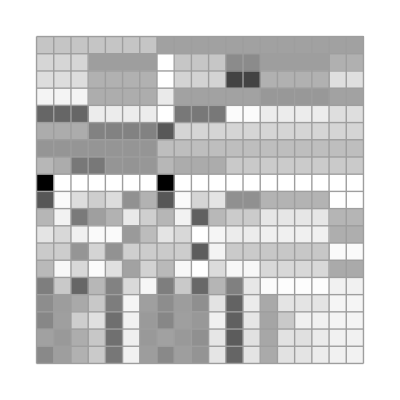

{1.,0.381966,0.381966,-0.381966,0.381966,-0.381966,0.145898,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
L=L/σ;
{λ,ρ}=Eigensystem[L/.σSol//N]//Chop;
ArrayPlot[ρ,Mesh->True]
λ
```

```mathematica
{UL,WL,VL}=SingularValueDecomposition[L/.σSol//N]//Chop;
```

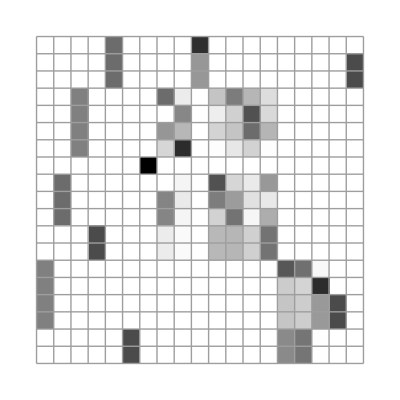

True

```mathematica
ArrayPlot[UL,Mesh->True]
Chop[UL.Transpose[UL]]==IdentityMatrix[Length[UL]]
```

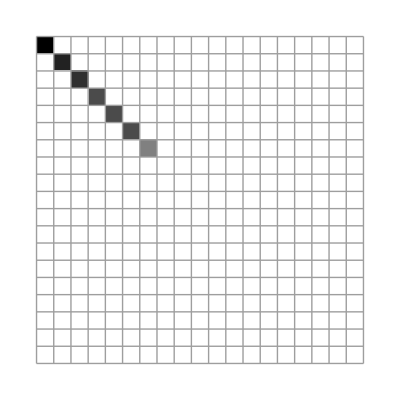

```mathematica
ArrayPlot[WL,Mesh->True]
```

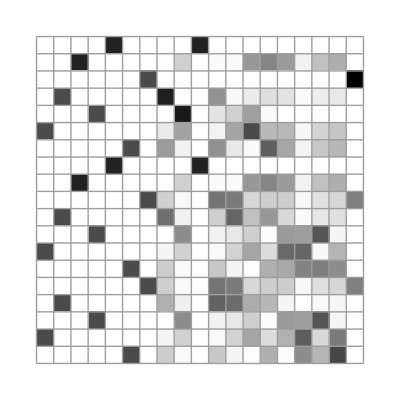

True

```mathematica
ArrayPlot[VL,Mesh->True]
Chop[VL.Transpose[VL]]==IdentityMatrix[Length[UL]]
```

```mathematica
(L/.σSol//N)==UL.WL.Transpose[VL]
```

True

```mathematica
SingularValueList[L]
```

{2 √3 √(1/(σ Conjugate[σ])),3 √(1/(σ Conjugate[σ])),2 √2 √(1/(σ Conjugate[σ])),√6 √(1/(σ Conjugate[σ])),√6 √(1/(σ Conjugate[σ])),√6 √(1/(σ Conjugate[σ])),√3 √(1/(σ Conjugate[σ]))}

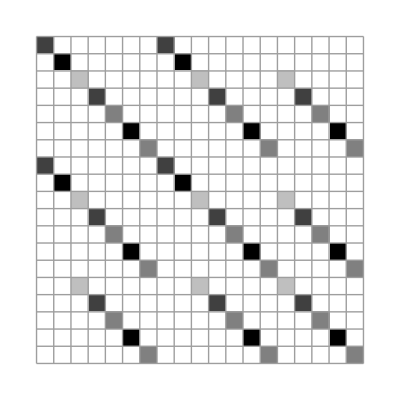

{{1.75078,1.31308,1.16718,0.875388,0.875388,0.875388,0.437694,0,0,0,0,0,0,0,0,0,0,0,0},{{0,0,0,0,0,-0.57735,0,0,0,0,0,0,-0.57735,0,0,0,0,-0.57735,0},{0,0,0,0.57735,0,0,0,0,0,0,0.57735,0,0,0,0,0.57735,0,0,0},{0,0.707107,0,0,0,0,0,0,0.707107,0,0,0,0,0,0,0,0,0,0},{-0.707107,0,0,0,0,0,0,-0.707107,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-0.57735,0,0,0,0,0,0,-0.57735,0,0,0,0,-0.57735,0,0},{0,0,0,0,0,0,-0.57735,0,0,0,0,0,0,-0.57735,0,0,0,0,-0.57735},{0,0,-0.57735,0,0,0,0,0,0,-0.57735,0,0,0,0,-0.57735,0,0,0,0},{0,-0.607222,0.13155,-0.0618713,0.0821065,0.309931,0.0397736,0,0.607222,-0.210652,0.0618713,-0.0821065,-0.269503,-0.0397736,0.0791016,0,0,-0.0404281,0},{0,0,0,0.408248,0,0,0,0,0,0,0.408248,0,0,0,0,-0.816497,0,0,0},{0,0,0.199104,0.00688999,0.357849,-0.230612,0.424859,0,0,0.163664,-0.00688999,-0.357849,-0.113803,-0.424859,-0.362768,0,0,0.344415,0},{0.586335,0.165735,-0.054775,-0.192747,0.143982,0.19697,-0.00189263,-0.586335,-0.165735,-0.117862,0.192747,-0.143982,-0.234174,0.00189263,0.172637,0,0,0.037204,0},{0,0,0,0,-0.408248,0,0,0,0,0,0,-0.408248,0,0,0,0,0.816497,0,0},{0,0,0,0,0,0,-0.408248,0,0,0,0,0,0,-0.408248,0,0,0,0,0.816497},{0.113462,-0.00219724,0.158252,-0.100455,-0.325914,0.347648,0.10215,-0.113462,0.00219724,0.414524,0.100455,0.325914,-0.0886301,-0.10215,-0.572776,0,0,-0.259017,0},{0,0,-0.167715,-0.0086491,-0.449213,-0.121626,0.338778,0,0,-0.123226,0.0086491,0.449213,-0.268258,-0.338778,0.290942,0,0,0.389884,0},{-0.363584,0.296341,0.0466247,-0.16761,0.12266,0.489555,0.0419778,0.363584,-0.296341,-0.134973,0.16761,-0.12266,-0.447859,-0.0419778,0.0883482,0,0,-0.0416959,0},{0.0403031,-0.0293608,-0.452402,0.451419,0.0933605,0.222369,-0.0776085,-0.0403031,0.0293608,0.417037,-0.451419,-0.0933605,-0.339198,0.0776085,0.0353657,0,0,0.116828,0},{0.0975704,0.122998,0.505749,0.464058,-0.0677266,0.144472,0.0810676,-0.0975704,-0.122998,-0.448991,-0.464058,0.0677266,-0.0184736,-0.0810676,-0.0567574,0,0,-0.125998,0},{0,0,-0.301535,0.0398052,0.0900623,0.181644,0.422311,0,0,0.02949,-0.0398052,-0.0900623,0.361185,-0.422311,0.272045,0,0,-0.54283,0}}}

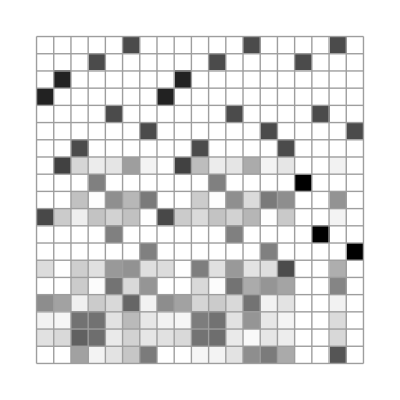

```mathematica
ArrayPlot[Chop[Transpose[(L/.σSol//N)].(L/.σSol//N)],Mesh-> True]
Eigensystem[Chop[Transpose[(L/.σSol//N)].(L/.σSol//N)]]//Chop
ArrayPlot[%[[2]],Mesh-> True]
```

#### Period 2 periodic point n=19 partition - Spectral decomposition

```mathematica
CharacteristicPolynomial[L,z]
Factor[%]
```

-z^19+z^12/σ^7-(4 z^13)/σ^6+(2 z^14)/σ^5+(7 z^15)/σ^4-(7 z^16)/σ^3-(2 z^17)/σ^2+(4 z^18)/σ

-(z^12 (-1+z σ)^3 (1+z σ)^2 (1-3 z σ+z^2 σ^2))/σ^7

```mathematica
circle1=Graphics[Circle[{0,0},1]];
circle2=Graphics[Circle[{0,0},1/σ//N]];
circle3=Graphics[Circle[{0,0},1/σ^2//N]];
circle4=Graphics[Circle[{0,0},1/σ^3//N]];
circle5=Graphics[Circle[{0,0},1/σ^4//N]];
```

```mathematica
Table[{i,λ[[i]],Abs[λ[[i]]]},{i,Length[λ]}]//Chop
```

{{1,1.,1.},{2,0.381966,0.381966},{3,0.381966,0.381966},{4,-0.381966,0.381966},{5,0.381966,0.381966},{6,-0.381966,0.381966},{7,0.145898,0.145898},{8,0,0},{9,0,0},{10,0,0},{11,0,0},{12,0,0},{13,0,0},{14,0,0},{15,0,0},{16,0,0},{17,0,0},{18,0,0},{19,0,0}}

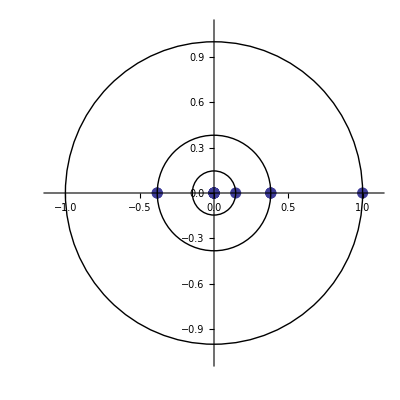

```mathematica
Show[ListPlot[{Re[#],Im[#]}&/@λ//N,AspectRatio->Automatic,PlotRange->{{-1.1,1.1},{-1.1,1.1}},ImageSize->Scaled[0.5],PlotStyle->PointSize[0.02]],circle1,circle2,circle3]/.σSol//N
```

```mathematica
plotEigenstate[ψ_,fenceFlag_]:=Module[
{Rsteps = {Line[{{gridPoint[[1]],Re[ψ[[1]]]},{gridPoint[[2]],Re[ψ[[1]]]}}]},
Isteps = {Line[{{gridPoint[[1]],Im[ψ[[1]]]},{gridPoint[[2]],Im[ψ[[1]]]}}]},
min1=1.1Min[Min[Re[ψ]],0],max1=1.1Max[Max[Re[ψ]],0],
min2=1.1Min[Min[Im[ψ]],0],max2=1.1Max[Max[Im[ψ]],0]},
Do[
Rsteps = Append[Rsteps,
Line[{{gridPoint[[i]],Re[ψ[[i]]]},{gridPoint[[i+1]],Re[ψ[[i]]]}}]
];
Isteps = Append[Isteps,
Line[{{gridPoint[[i]],Im[ψ[[i]]]},{gridPoint[[i+1]],Im[ψ[[i]]]}}]
],
{i,2,Length[gridPoint]-1}];
Rfence=Ifence=Rfence2=Ifence2=Graphics[Point[{0,0}]];
If[fenceFlag,
Rfence=Table[Graphics[Line[{{gridPoint[[i]],min1},{gridPoint[[i]],max1}}]],{i,2,Length[a]}];Ifence=Table[Graphics[Line[{{gridPoint[[i]],min2},{gridPoint[[i]],max2}}]],{i,2,Length[a]}];
Rfence2=Table[Graphics[{Thick,Line[{{gridPeriodicPoint[[i]],min1},{gridPeriodicPoint[[i]],max1}}]}],{i,Length[gridPeriodicPoint]}];
Ifence2=Table[Graphics[{Thick,Line[{{gridPeriodicPoint[[i]],min2},{gridPeriodicPoint[[i]],max2}}]}],{i,Length[gridPeriodicPoint]}]
];
GraphicsGrid[{{
Show[ListPlot[Table[{gridPoint[[i+1]],Re[ψ[[i]]]},{i,Length[ψ]}],ImageSize->Scaled[1],Axes->False,PlotStyle->PointSize[0.001],Frame->True,PlotRange->{{0,A2/.A2Sol//N},{min1,max1}}],Graphics[Rsteps],Rfence,Rfence2],
Show[ListPlot[Table[{gridPoint[[i+1]],Im[ψ[[i]]]},{i,Length[ψ]}],ImageSize->Scaled[1],
Axes->False,PlotStyle->PointSize[0.001],Frame->True,PlotRange->{{0,A2/.A2Sol//N},{min2,max2}}],Graphics[Isteps],Ifence,Ifence2]
}}]
]
```

```mathematica
measure[ψ_] :=
Sum[Re[ψ[[i]]](gridPoint[[i+1]]-gridPoint[[i]]),{i,Length[ψ]}]//Chop
measureA[ψ_] :=
Abs@Sum[Re[ψ[[i]]](gridPoint[[i+1]]-gridPoint[[i]]),{i,iAlpha-1}]//Chop
measureB[ψ_] :=
Abs@Sum[Re[ψ[[i]]](gridPoint[[i+1]]-gridPoint[[i]]),{i,iAlpha,Length[ψ]}]//Chop
```

As expected the eigenvectors of Perron-Frobenius with non vanishing eigenvalue are elements of 𝕊(𝔓^2), that is ℒ (𝕊𝔓^(*2)) ⊂ 𝕊(𝔓^2).

1

1.

0.306887

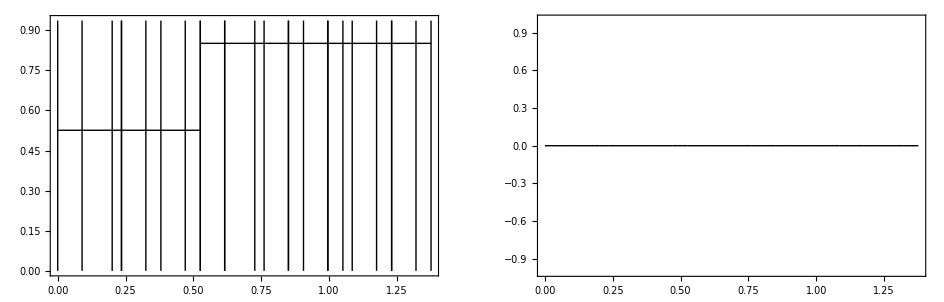

```mathematica
l=1
λ[[l]]
norm=measure[ρ[[l]]]
ρ[[l]]=ρ[[l]]/norm;
plotEigenstate[ρ[[l]],True]
```

2

0.381966

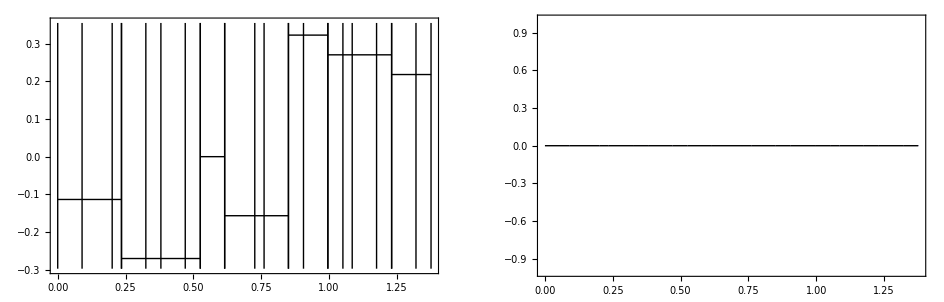

3

0.381966

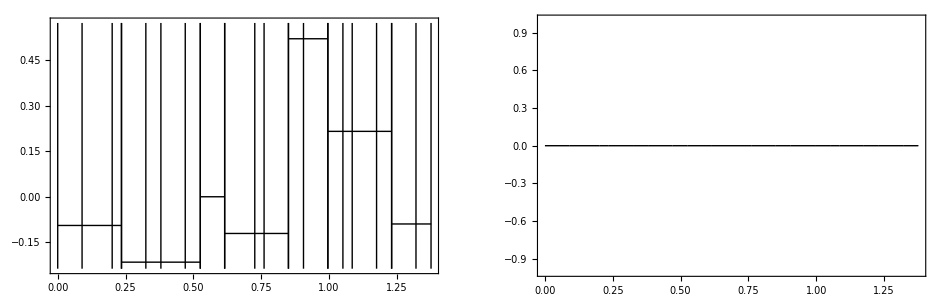

5

0.381966

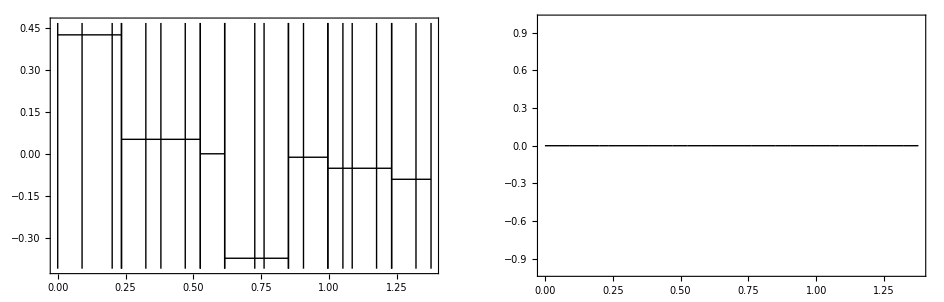

```mathematica
l=2
λ[[l]]
plotEigenstate[ρ[[l]],True]
l=3
λ[[l]]
plotEigenstate[ρ[[l]],True]
l=5
λ[[l]]
plotEigenstate[ρ[[l]],True]
```

4

-0.381966

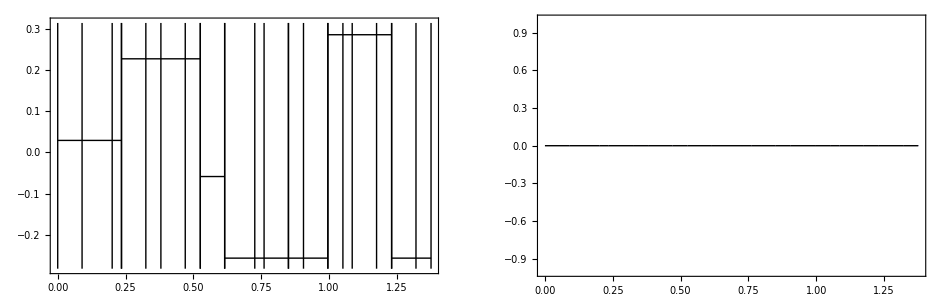

6

-0.381966

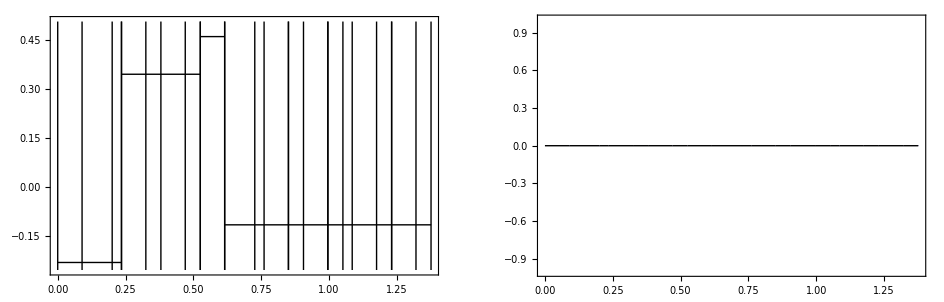

```mathematica
l=4
λ[[l]]
plotEigenstate[ρ[[l]],True]
l=6
λ[[l]]
plotEigenstate[ρ[[l]],True]
```

7

0.145898

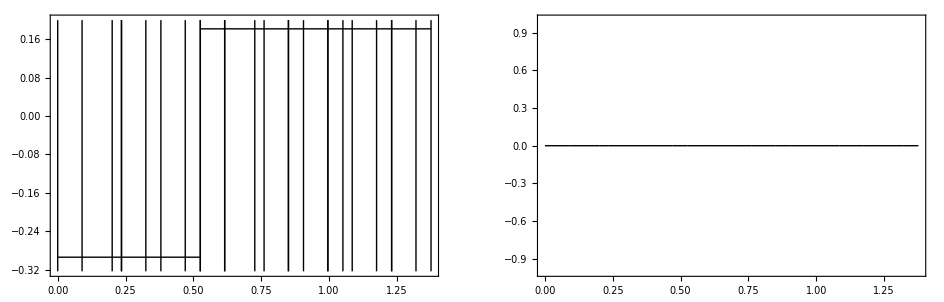

```mathematica
l=7
λ[[l]]
plotEigenstate[ρ[[l]],True]
```

And the eigenvectors of Perron-Frobenius spanning the kernel of the operator are elements of 𝕊𝔓^(*2) because ℒ (𝕊𝔓^(*2)) ⊂ 𝕊(𝔓^2) ⊂ 𝕊𝔓^(*2)

8

0

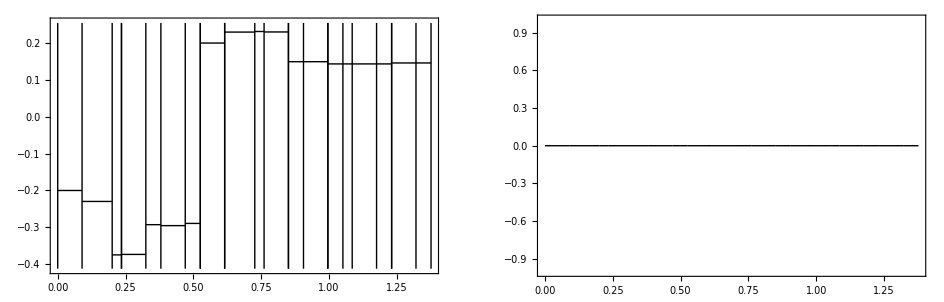

9

0

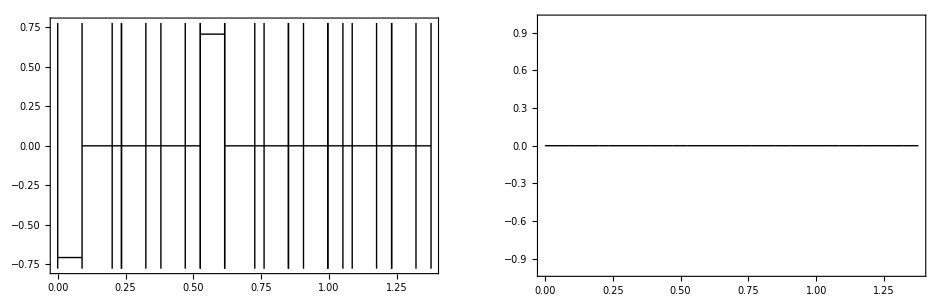

10

0

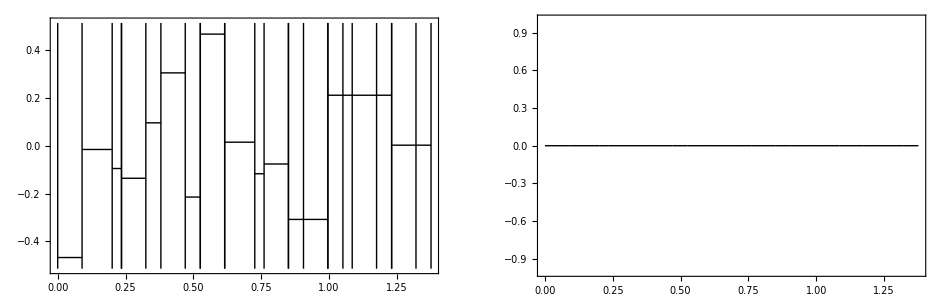

11

0

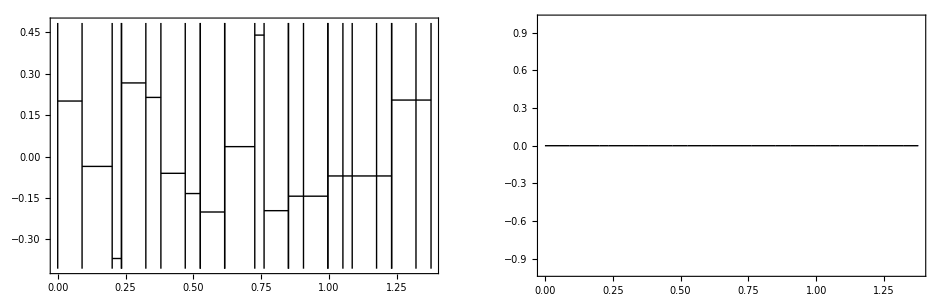

12

0

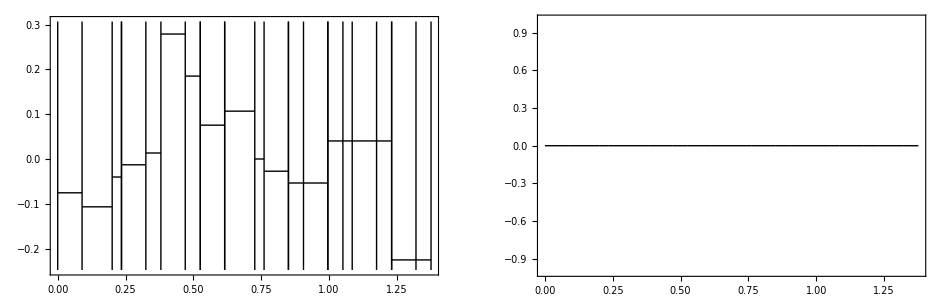

13

0

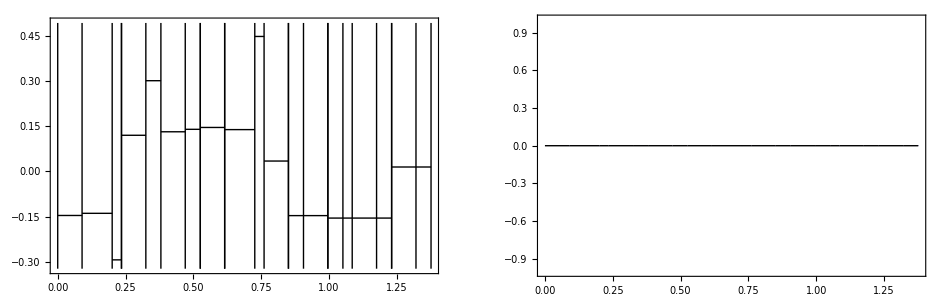

14

0

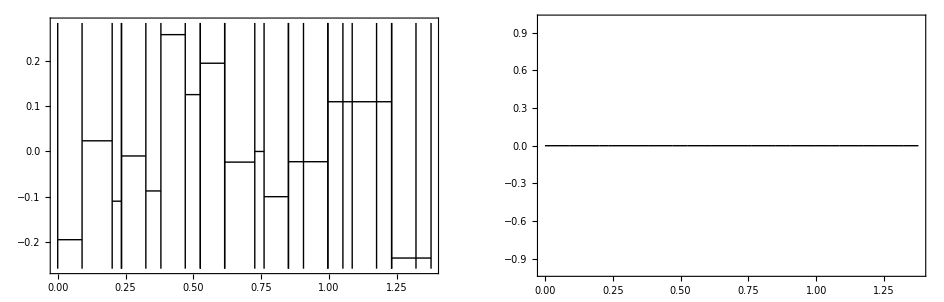

15

0

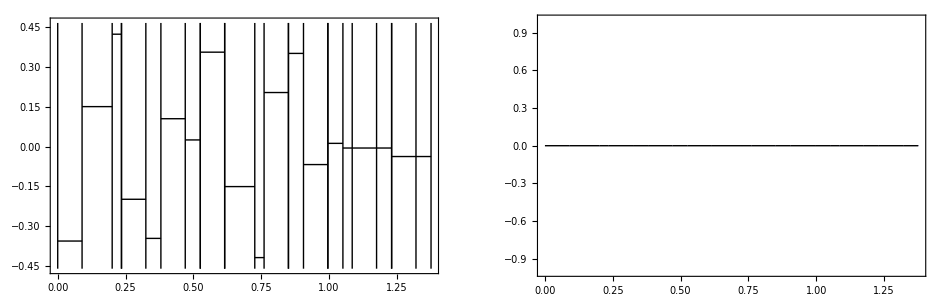

16

0

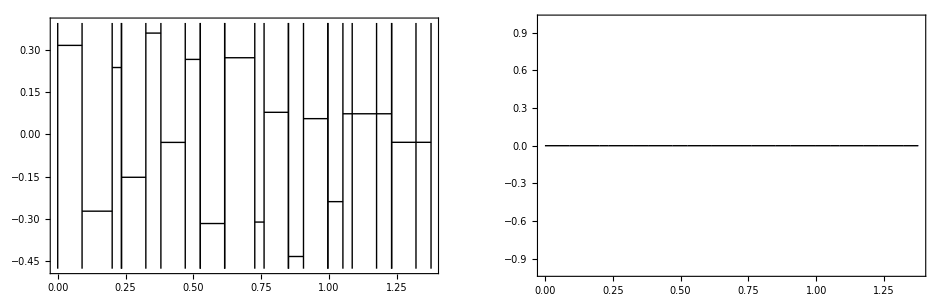

17

0

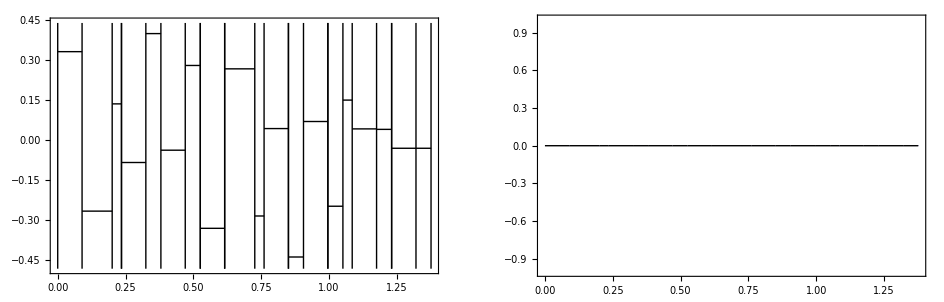

18

0

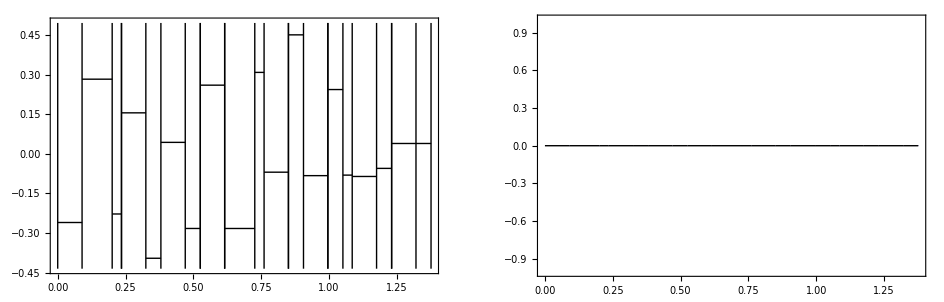

19

0

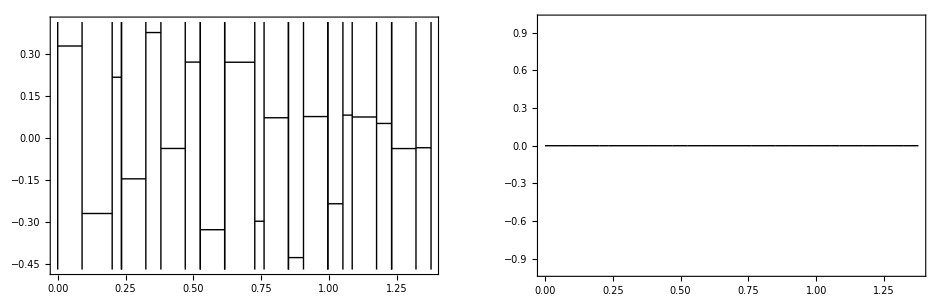

```mathematica
Do[
Print[l];
Print[λ[[l]]];
Print@plotEigenstate[ρ[[l]],True],
{l,8,Length[λ]}]
```

#### Period 2 periodic point n=19 partition - Dual Space

```mathematica
Clear[c,χ]
χ = Table[c[i,j],{i,Length[L]},{j,Length[L]}];
χSol=Solve[Table[χ[[i]].ρ[[j]]==If[i==j,1,0],{i,Length[L]},{j,Length[L]}]//Flatten,χ//Flatten]//Chop;
```

1

1.

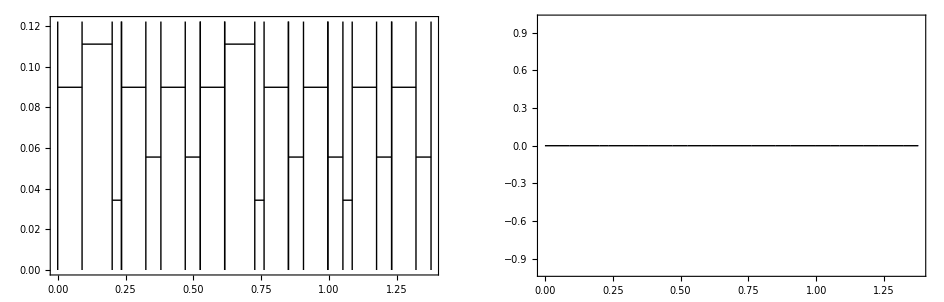

```mathematica
l=1
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],True]
```

2

0.381966

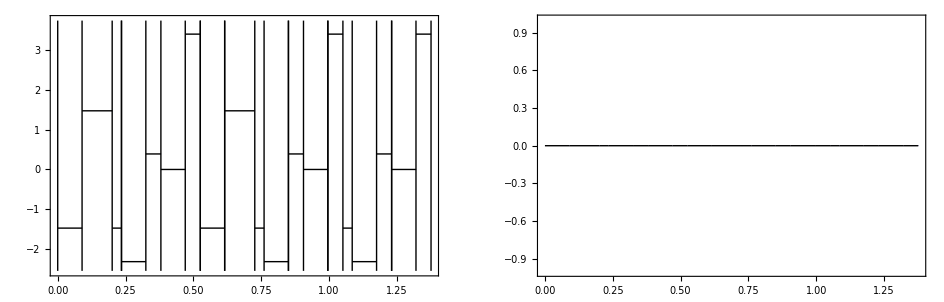

3

0.381966

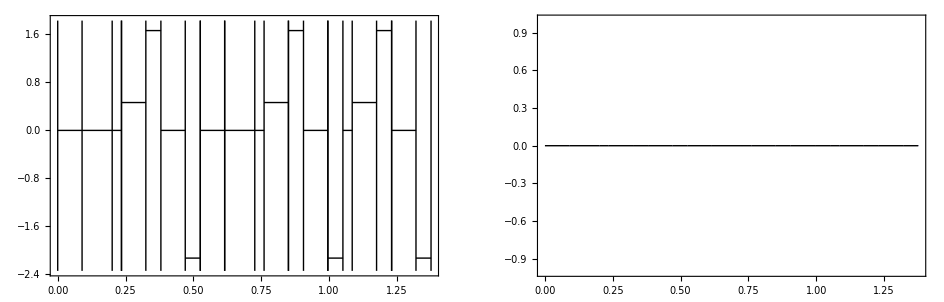

5

0.381966

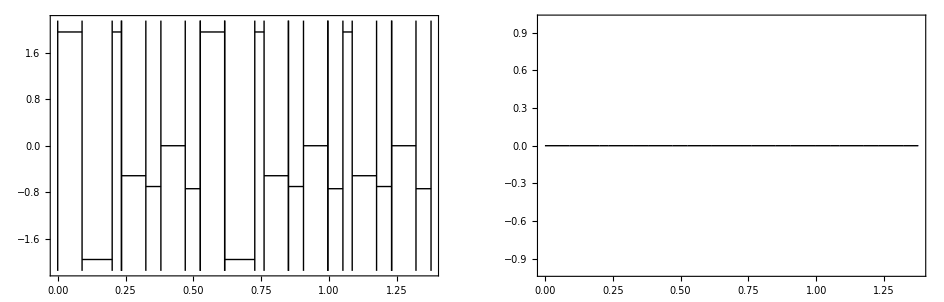

```mathematica
l=2
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],True]
l=3
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],True]
l=5
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],True]
```

4

-0.381966

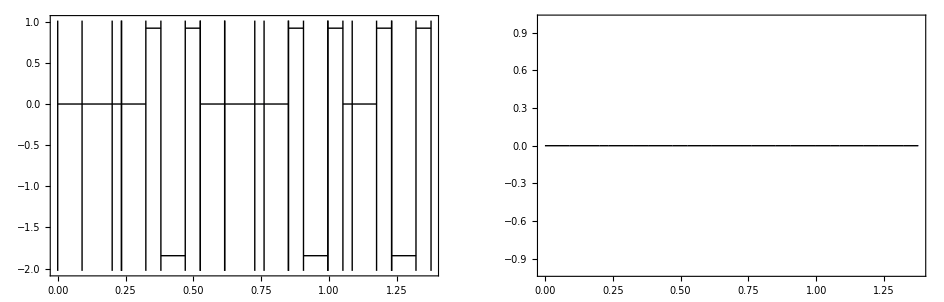

6

-0.381966

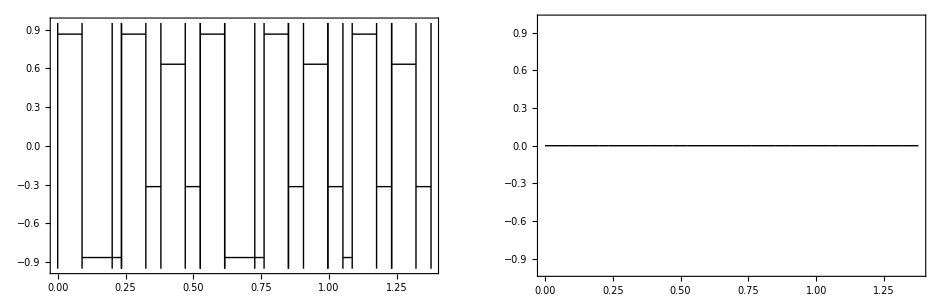

```mathematica
l=4
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],True]
l=6
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],True]
```

7

0.145898

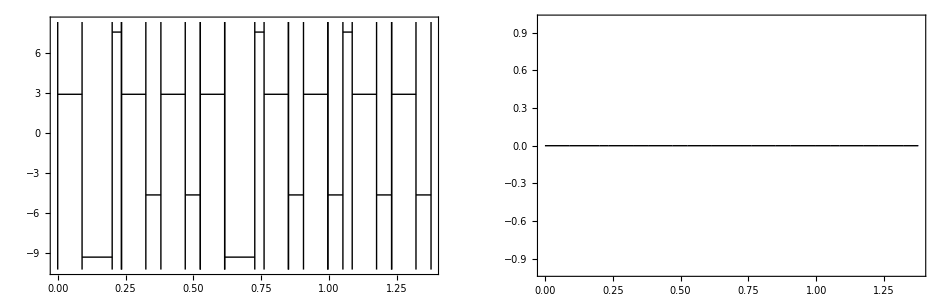

```mathematica
l=7
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],True]
```

8

0

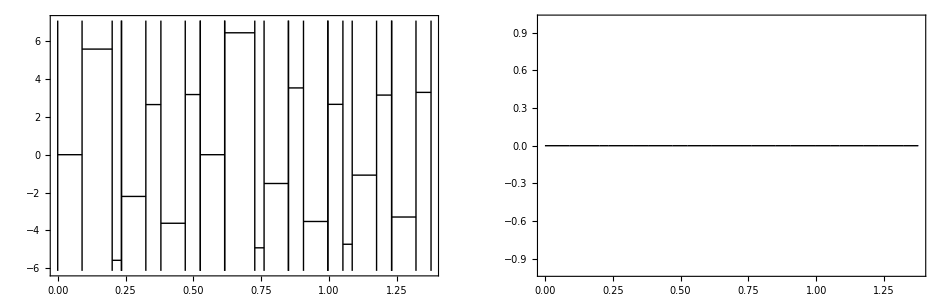

9

0

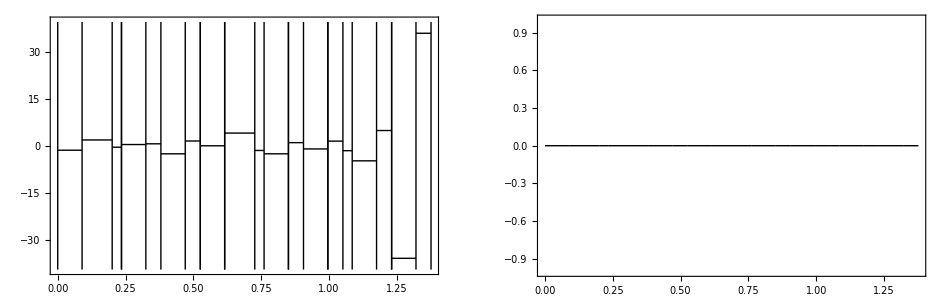

10

0

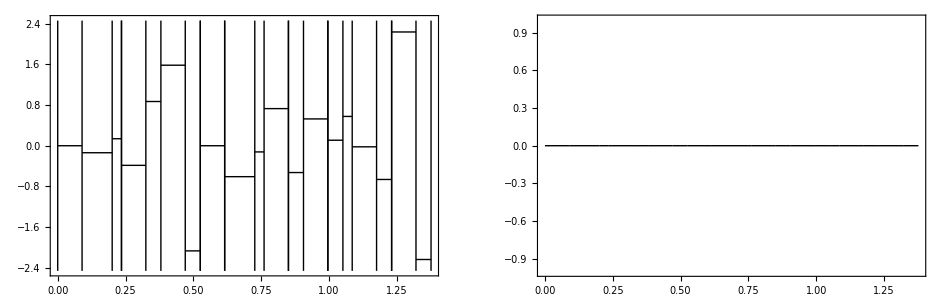

11

0

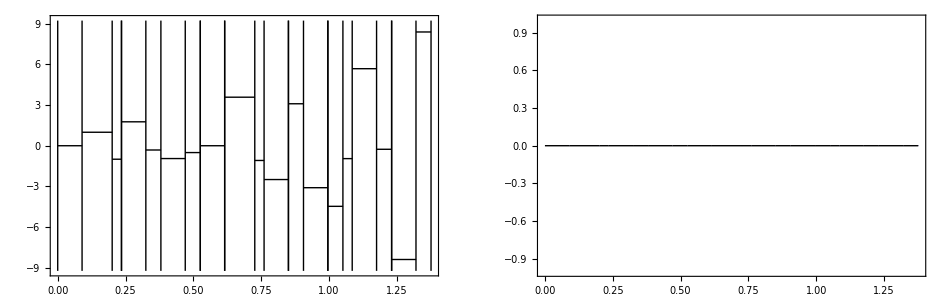

12

0

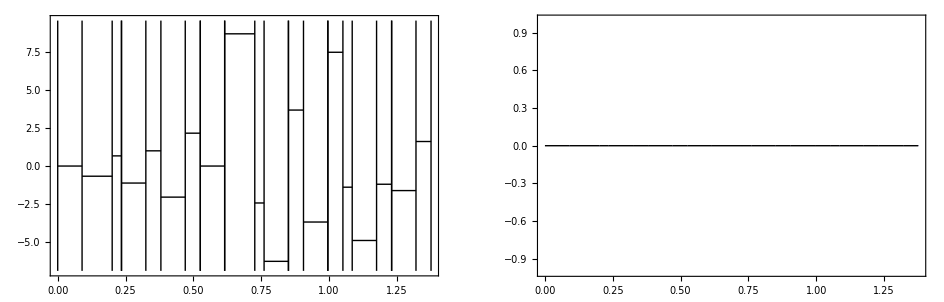

13

0

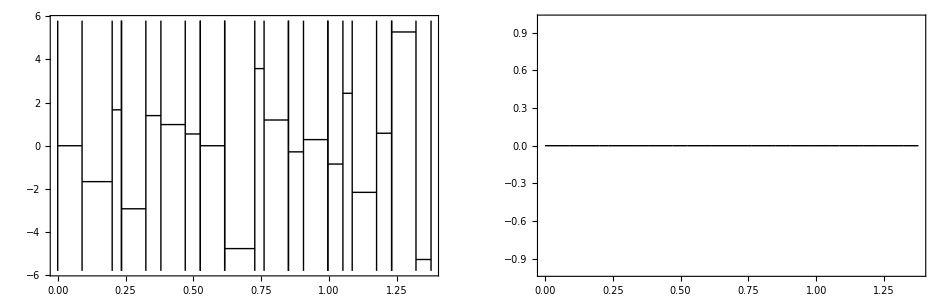

14

0

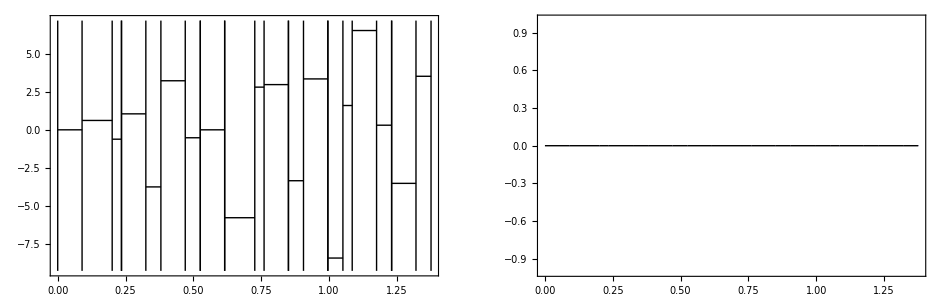

15

0

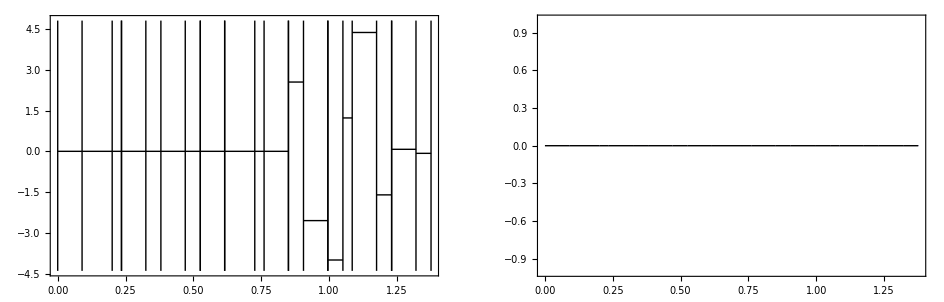

16

0

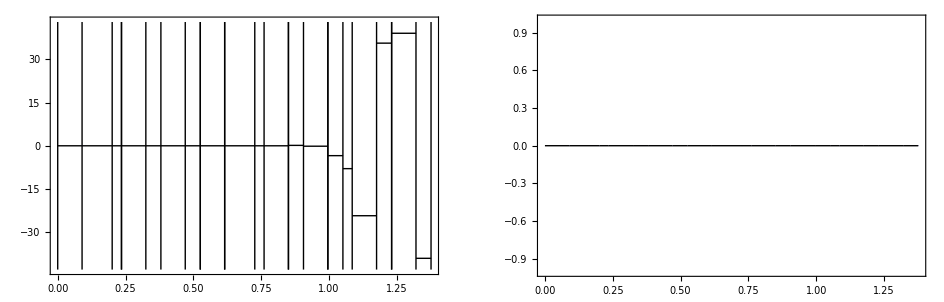

17

0

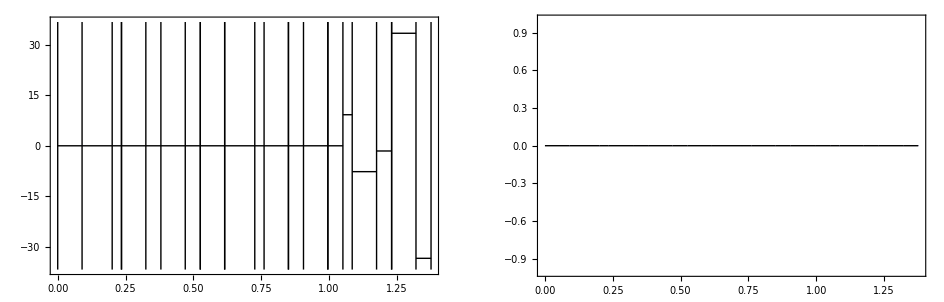

18

0

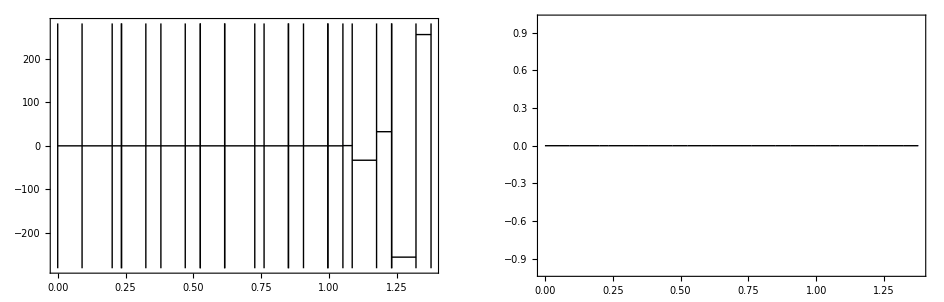

19

0

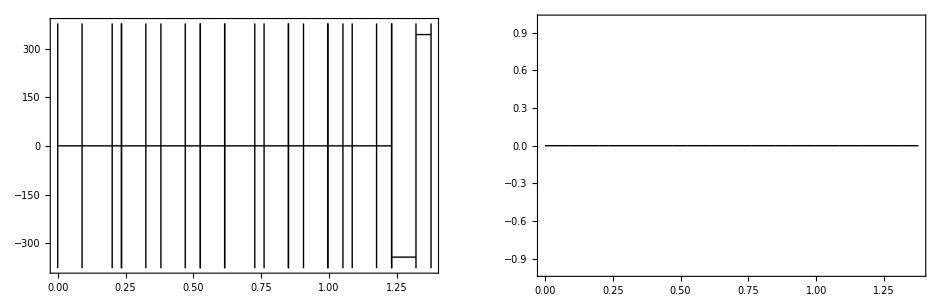

```mathematica
Do[
Print[l];
Print[λ[[l]]];
Print@plotEigenstate[χ[[l]]/.χSol[[1]],True],
{l,8,Length[λ]}]
```

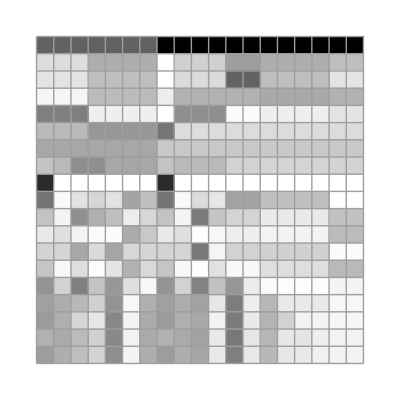

0

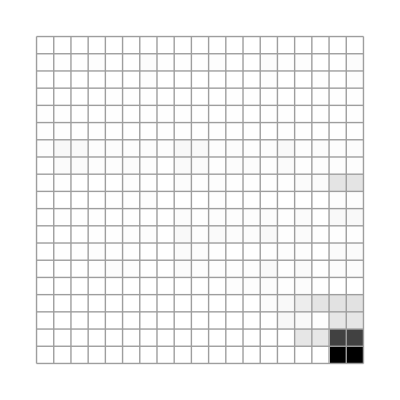

1.7583×10^11

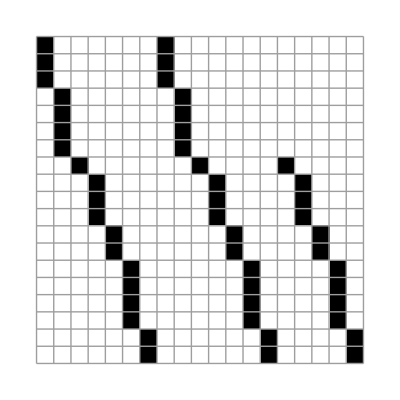

True

```mathematica
ArrayPlot[ρ//Chop,Mesh-> True]
Det[ρ]//Chop
ArrayPlot[χ/.χSol[[1]]//Chop,Mesh-> True]
Det[χ/.χSol[[1]]//Chop]//Chop
ArrayPlot[Transpose[ρ].DiagonalMatrix[λ].χ/.χSol[[1]]//Chop,Mesh-> True]
(L/.σSol//N)==Chop[Transpose[ρ].DiagonalMatrix[λ].χ/.χSol[[1]]]
```

#### Period 3 periodic point n=49 partition - Operator construction

```mathematica
gridPoint={0,0.08122992405822657,0.21266270208800997,0.29389262614623657,0.42532540417602,0.5257311121191336,0.5567581822058033,0.6379881062640298,0.6881909602355867,0.7694208842938133,0.8506508083520399,0.9008536623235966,0.9820835863818231,1.03228644035338,1.1135163644116066,1.1947462884698332,1.24494914244139,1.3261790664996165,1.3763819204711734}
Length[%]
```

{0,0.0812299,0.212663,0.293893,0.425325,0.525731,0.556758,0.637988,0.688191,0.769421,0.850651,0.900854,0.982084,1.03229,1.11352,1.19475,1.24495,1.32618,1.37638}

19

{0.619015,0.457167,1.08087,0.661371,0.532071,1.37473,0.451946,0.782786,0.808797,0.688091,1.30002,0.7515,0.446865,1.02008,1.20105,1.19694,0.383457,0.0164113}

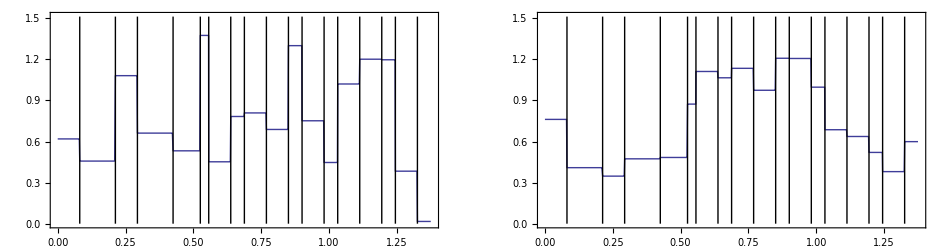

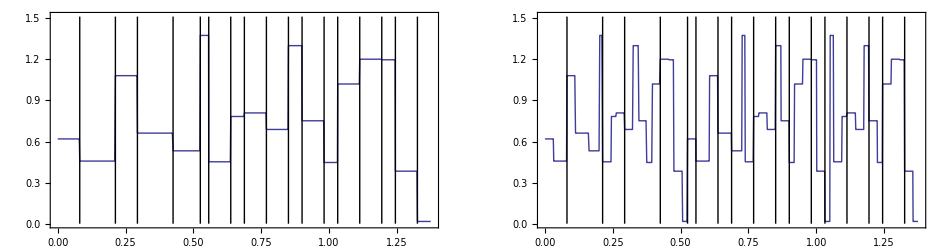

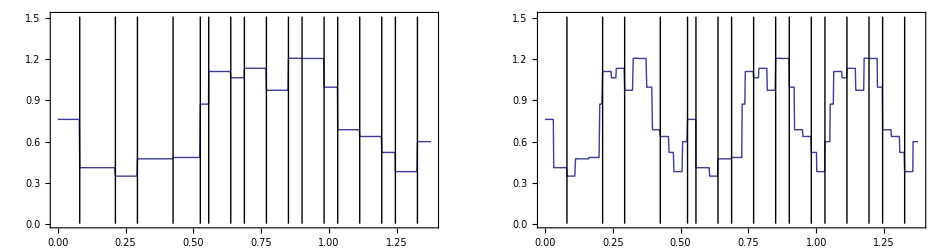

```mathematica
n=50;
a=Table[RandomReal[1],{Length[gridPoint]-1}];
a=a/Sum[a[[i]](gridPoint[[i+1]]-gridPoint[[i]]),{i,Length[a]}]//N
fence=Table[Graphics[Line[{{gridPoint[[i]],0},{gridPoint[[i]],1.1 Max[a]}}]],{i,2,Length[a]}];
scale=1;
{plotOfS,plotOfLS,plotOfKS,plotOfKLS}=mapStepFunctionAndPlotResult[];
GraphicsGrid[{{Show[plotOfS,fence],Show[plotOfLS,fence]}}]
GraphicsGrid[{{Show[plotOfS,fence],Show[plotOfKS,fence]}}]
GraphicsGrid[{{Show[plotOfLS,fence],Show[plotOfKLS,fence]}}]
```

```mathematica
gridPeriodicPoint=gridPoint
Length[%]
gridPoint={0.,0.03102707008666976,0.08122992405822657,0.11225699414489634,0.16245984811645317,0.20081141588622728,0.21266270208800997,0.2436897721746797,0.2628655560595668,0.29389262614623657,0.3249196962329063,0.34409548011779334,0.37512255020446306,0.39429833408935017,0.42532540417602,0.4563524742626897,0.47552825814757677,0.5065553282342464,0.5257311121191336,0.5567581822058033,0.6069610361773601,0.6379881062640298,0.6881909602355867,0.7265425280053608,0.7383938142071435,0.7694208842938133,0.7885966681787002,0.8196237382653699,0.8506508083520399,0.8698265922369268,0.8816778784387097,0.9008536623235966,0.9200294462084837,0.9318807324102666,0.9510565162951534,0.9629078024969363,0.9820835863818231,1.0012593702667103,1.013110656468493,1.03228644035338,1.0514622242382672,1.06331351044005,1.0943405805267197,1.1135163644116066,1.1445434344982766,1.1755705045849463,1.1947462884698332,1.225773358556503,1.24494914244139,1.27597621252806,1.3070032826147298,1.3261790664996165,1.3572061365862864,1.3763819204711734}
Length[%]
```

{0,0.0812299,0.212663,0.293893,0.425325,0.525731,0.556758,0.637988,0.688191,0.769421,0.850651,0.900854,0.982084,1.03229,1.11352,1.19475,1.24495,1.32618,1.37638}

19

{0.,0.0310271,0.0812299,0.112257,0.16246,0.200811,0.212663,0.24369,0.262866,0.293893,0.32492,0.344095,0.375123,0.394298,0.425325,0.456352,0.475528,0.506555,0.525731,0.556758,0.606961,0.637988,0.688191,0.726543,0.738394,0.769421,0.788597,0.819624,0.850651,0.869827,0.881678,0.900854,0.920029,0.931881,0.951057,0.962908,0.982084,1.00126,1.01311,1.03229,1.05146,1.06331,1.09434,1.11352,1.14454,1.17557,1.19475,1.22577,1.24495,1.27598,1.307,1.32618,1.35721,1.37638}

54

{0.257054,0.638562,1.21396,1.19748,0.351266,0.384599,0.344488,0.428536,0.739533,0.475743,1.26908,0.360706,0.455315,0.662967,1.34098,1.0823,0.358801,0.127624,0.89984,0.38793,1.06752,0.110872,1.03291,1.04924,1.15363,0.0325001,1.1699,0.978659,1.25343,0.345962,1.33987,0.210088,1.32849,1.30365,1.1337,1.05193,1.35147,0.417153,0.766549,0.0217039,0.0464517,0.382676,1.23975,0.064337,0.964684,0.522415,0.907334,0.940069,0.428811,0.945964,0.7051,0.951413,0.905497}

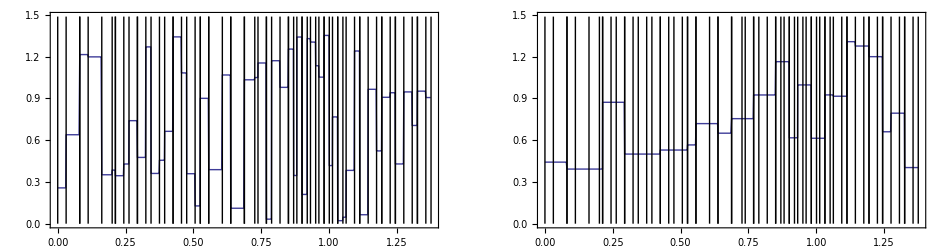

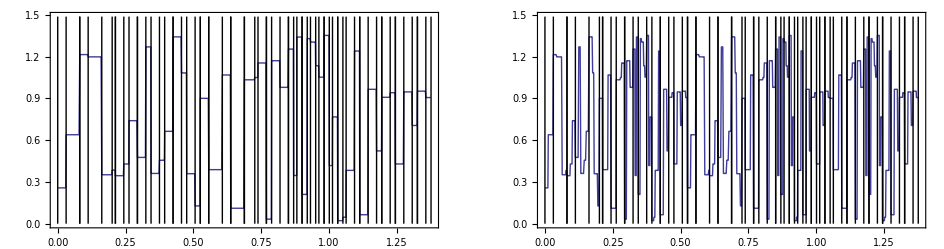

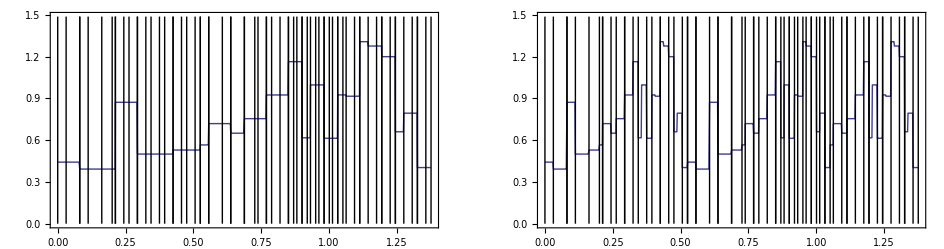

```mathematica
n=20;
a=Table[RandomReal[1],{Length[gridPoint]-1}];
a=a/Sum[a[[i]](gridPoint[[i+1]]-gridPoint[[i]]),{i,Length[a]}]//N
fence=Table[Graphics[Line[{{gridPoint[[i]],0},{gridPoint[[i]],1.1 Max[a]}}]],{i,2,Length[a]}];
fence2=Table[Graphics[{Thick,Line[{{gridPeriodicPoint[[i]],0},{gridPeriodicPoint[[i]],1.1 Max[a]}}]}],{i,Length[gridPeriodicPoint]}];
{plotOfS,plotOfLS,plotOfKS,plotOfKLS}=mapStepFunctionAndPlotResult[];
GraphicsGrid[{{Show[plotOfS,fence,fence2],Show[plotOfLS,fence,fence2]}}]
GraphicsGrid[{{Show[plotOfS,fence,fence2],Show[plotOfKS,fence,fence2]}}]
GraphicsGrid[{{Show[plotOfLS,fence,fence2],Show[plotOfKLS,fence,fence2]}}]
```

```mathematica
cellList=Transpose[{Table[i-1,{i,Length[gridPoint]}],gridPoint}]
L=Table[0,{Length[gridPoint]-1},{Length[gridPoint]-1}];
Do[
Print[i];
interval={gridPoint[[i]]/σ,gridPoint[[i+1]]/σ}/.varSol//N;
cell=cellFind[interval];
Print[interval,"->",cell];
L[[i,cell]]=1;
interval={gridPoint[[i]]/σ+α,gridPoint[[i+1]]/σ+α}/.varSol//N;
cell=cellFind[interval];
Print[interval,"->",cell];
L[[i,cell]]=1;
If[gridPoint[[i]]≥ α/.varSol//N,
interval={gridPoint[[i]]/σ+β,gridPoint[[i+1]]/σ+β}/.varSol//N;
cell=cellFind[interval];
Print[interval,"->",cell]];
  L[[i,cell]]=1,
{i,Length[gridPoint]-1}]
ArrayPlot[L,Mesh->True]
```

{{0,0.},{1,0.0310271},{2,0.0812299},{3,0.112257},{4,0.16246},{5,0.200811},{6,0.212663},{7,0.24369},{8,0.262866},{9,0.293893},{10,0.32492},{11,0.344095},{12,0.375123},{13,0.394298},{14,0.425325},{15,0.456352},{16,0.475528},{17,0.506555},{18,0.525731},{19,0.556758},{20,0.606961},{21,0.637988},{22,0.688191},{23,0.726543},{24,0.738394},{25,0.769421},{26,0.788597},{27,0.819624},{28,0.850651},{29,0.869827},{30,0.881678},{31,0.900854},{32,0.920029},{33,0.931881},{34,0.951057},{35,0.962908},{36,0.982084},{37,1.00126},{38,1.01311},{39,1.03229},{40,1.05146},{41,1.06331},{42,1.09434},{43,1.11352},{44,1.14454},{45,1.17557},{46,1.19475},{47,1.22577},{48,1.24495},{49,1.27598},{50,1.307},{51,1.32618},{52,1.35721},{53,1.37638}}

1

{0.,0.0118513}->1

{0.525731,0.537582}->19

2

{0.0118513,0.0310271}->1

{0.537582,0.556758}->19

3

{0.0310271,0.0428784}->2

{0.556758,0.568609}->20

4

{0.0428784,0.0620541}->2

{0.568609,0.587785}->20

5

{0.0620541,0.0767031}->2

{0.587785,0.602434}->20

6

{0.0767031,0.0812299}->2

{0.602434,0.606961}->20

7

{0.0812299,0.0930812}->3

{0.606961,0.618812}->21

8

{0.0930812,0.100406}->3

{0.618812,0.626137}->21

9

{0.100406,0.112257}->3

{0.626137,0.637988}->21

10

{0.112257,0.124108}->4

{0.637988,0.649839}->22

11

{0.124108,0.131433}->4

{0.649839,0.657164}->22

12

{0.131433,0.143284}->4

{0.657164,0.669015}->22

13

{0.143284,0.150609}->4

{0.669015,0.67634}->22

14

{0.150609,0.16246}->4

{0.67634,0.688191}->22

15

{0.16246,0.174311}->5

{0.688191,0.700042}->23

16

{0.174311,0.181636}->5

{0.700042,0.707367}->23

17

{0.181636,0.193487}->5

{0.707367,0.719218}->23

18

{0.193487,0.200811}->5

{0.719218,0.726543}->23

19

{0.200811,0.212663}->6

{0.726543,0.738394}->24

{1.05146,1.06331}->41

20

{0.212663,0.231838}->7

{0.738394,0.75757}->25

{1.06331,1.08249}->42

21

{0.231838,0.24369}->7

{0.75757,0.769421}->25

{1.08249,1.09434}->42

22

{0.24369,0.262866}->8

{0.769421,0.788597}->26

{1.09434,1.11352}->43

23

{0.262866,0.277515}->9

{0.788597,0.803246}->27

{1.11352,1.12817}->44

24

{0.277515,0.282041}->9

{0.803246,0.807772}->27

{1.12817,1.13269}->44

25

{0.282041,0.293893}->9

{0.807772,0.819624}->27

{1.13269,1.14454}->44

26

{0.293893,0.301217}->10

{0.819624,0.826948}->28

{1.14454,1.15187}->45

27

{0.301217,0.313068}->10

{0.826948,0.8388}->28

{1.15187,1.16372}->45

28

{0.313068,0.32492}->10

{0.8388,0.850651}->28

{1.16372,1.17557}->45

29

{0.32492,0.332244}->11

{0.850651,0.857975}->29

{1.17557,1.1829}->46

30

{0.332244,0.336771}->11

{0.857975,0.862502}->29

{1.1829,1.18742}->46

31

{0.336771,0.344095}->11

{0.862502,0.869827}->29

{1.18742,1.19475}->46

32

{0.344095,0.35142}->12

{0.869827,0.877151}->30

{1.19475,1.20207}->47

33

{0.35142,0.355947}->12

{0.877151,0.881678}->30

{1.20207,1.2066}->47

34

{0.355947,0.363271}->12

{0.881678,0.889002}->31

{1.2066,1.21392}->47

35

{0.363271,0.367798}->12

{0.889002,0.893529}->31

{1.21392,1.21845}->47

36

{0.367798,0.375123}->12

{0.893529,0.900854}->31

{1.21845,1.22577}->47

37

{0.375123,0.382447}->13

{0.900854,0.908178}->32

{1.22577,1.2331}->48

38

{0.382447,0.386974}->13

{0.908178,0.912705}->32

{1.2331,1.23762}->48

39

{0.386974,0.394298}->13

{0.912705,0.920029}->32

{1.23762,1.24495}->48

40

{0.394298,0.401623}->14

{0.920029,0.927354}->33

{1.24495,1.25227}->49

41

{0.401623,0.40615}->14

{0.927354,0.931881}->33

{1.25227,1.2568}->49

42

{0.40615,0.418001}->14

{0.931881,0.943732}->34

{1.2568,1.26865}->49

43

{0.418001,0.425325}->14

{0.943732,0.951057}->34

{1.26865,1.27598}->49

44

{0.425325,0.437177}->15

{0.951057,0.962908}->35

{1.27598,1.28783}->50

45

{0.437177,0.449028}->15

{0.962908,0.974759}->36

{1.28783,1.29968}->50

46

{0.449028,0.456352}->15

{0.974759,0.982084}->36

{1.29968,1.307}->50

47

{0.456352,0.468204}->16

{0.982084,0.993935}->37

{1.307,1.31885}->51

48

{0.468204,0.475528}->16

{0.993935,1.00126}->37

{1.31885,1.32618}->51

49

{0.475528,0.48738}->17

{1.00126,1.01311}->38

{1.32618,1.33803}->52

50

{0.48738,0.499231}->17

{1.01311,1.02496}->39

{1.33803,1.34988}->52

51

{0.499231,0.506555}->17

{1.02496,1.03229}->39

{1.34988,1.35721}->52

52

{0.506555,0.518407}->18

{1.03229,1.04414}->40

{1.35721,1.36906}->53

53

{0.518407,0.525731}->18

{1.04414,1.05146}->40

{1.36906,1.37638}->53

-Graphics-

```mathematica
gridPoint={0.,0.03102707008666976,0.08122992405822657,0.11225699414489634,0.16245984811645317,0.20081141588622728,0.21266270208800997,0.2436897721746797,0.2628655560595668,0.29389262614623657,0.3249196962329063,0.34409548011779334,0.37512255020446306,0.39429833408935017,0.42532540417602,0.4563524742626897,0.47552825814757677,0.5065553282342464,0.5257311121191336,0.5567581822058033,0.6069610361773601,0.6379881062640298,0.6881909602355867,0.7265425280053608,0.7383938142071435,0.7694208842938133,0.7885966681787002,0.8196237382653699,0.8506508083520399,0.8698265922369268,(*0.8816778784387097,*)0.9008536623235966,0.9200294462084837,(*0.9318807324102666,*)0.9510565162951534,(*0.9629078024969363,*)0.9820835863818231,1.0012593702667103,(*1.013110656468493,*)1.03228644035338,1.0514622242382672,1.06331351044005,1.0943405805267197,1.1135163644116066,1.1445434344982766,1.1755705045849463,1.1947462884698332,1.225773358556503,1.24494914244139,1.27597621252806,1.3070032826147298,1.3261790664996165,1.3572061365862864,1.3763819204711734}
Length[%]
iAlpha=19;
```

{0.,0.0310271,0.0812299,0.112257,0.16246,0.200811,0.212663,0.24369,0.262866,0.293893,0.32492,0.344095,0.375123,0.394298,0.425325,0.456352,0.475528,0.506555,0.525731,0.556758,0.606961,0.637988,0.688191,0.726543,0.738394,0.769421,0.788597,0.819624,0.850651,0.869827,0.900854,0.920029,0.951057,0.982084,1.00126,1.03229,1.05146,1.06331,1.09434,1.11352,1.14454,1.17557,1.19475,1.22577,1.24495,1.27598,1.307,1.32618,1.35721,1.37638}

50

{0.052009,0.786325,1.43408,0.0175869,0.755109,0.525401,0.0595122,0.391368,0.818556,0.422943,0.328981,0.0967011,0.53753,0.545719,1.36439,0.831353,1.0682,1.15979,0.176528,0.820501,1.10047,0.832702,0.499041,0.762497,0.354627,0.718506,0.804181,1.434,0.58971,0.330398,0.743655,1.17342,0.640687,0.642178,1.38829,1.1237,1.018,0.544982,0.168514,0.223832,0.982695,0.263387,1.3357,1.15432,1.23899,0.752898,0.997968,1.22885,0.462689}

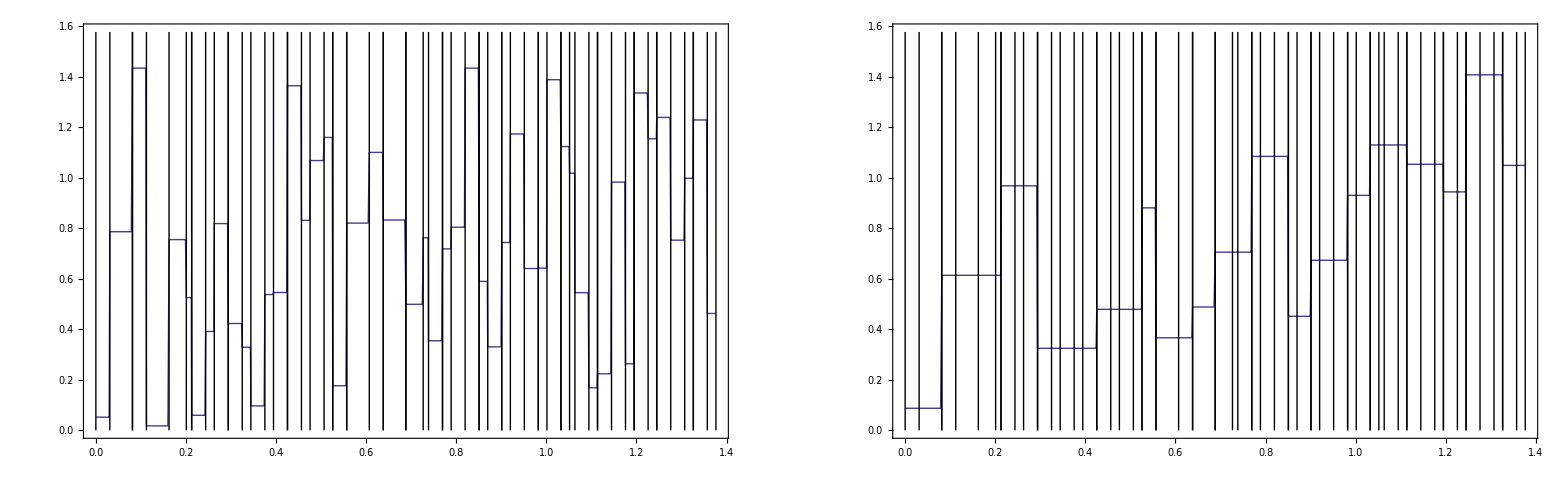

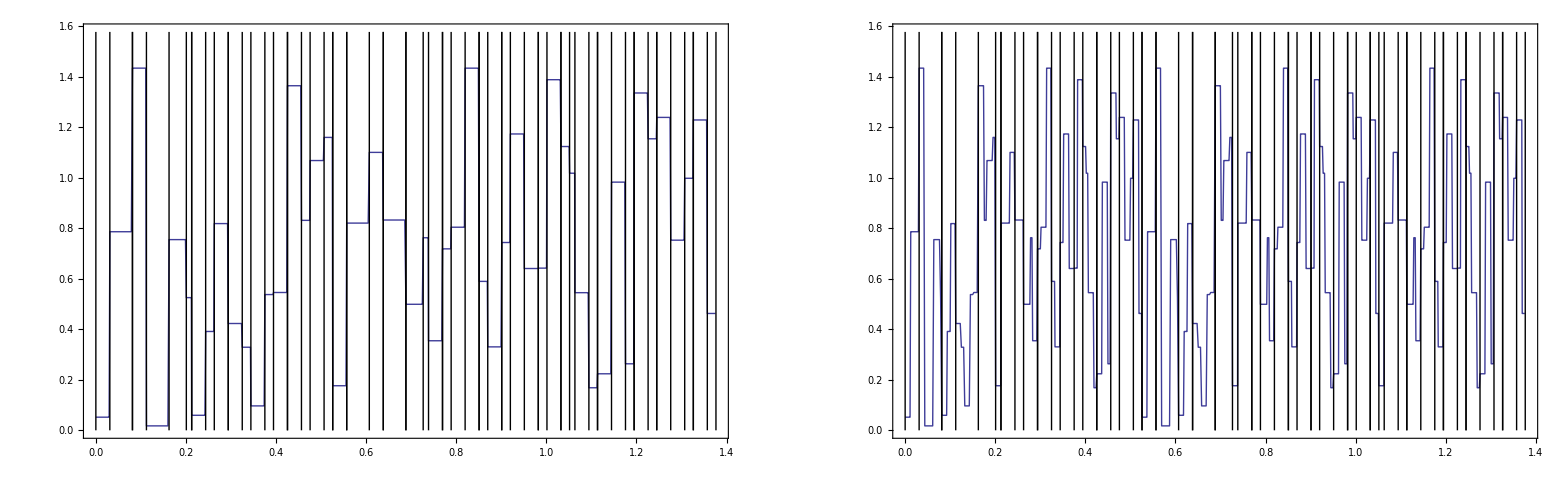

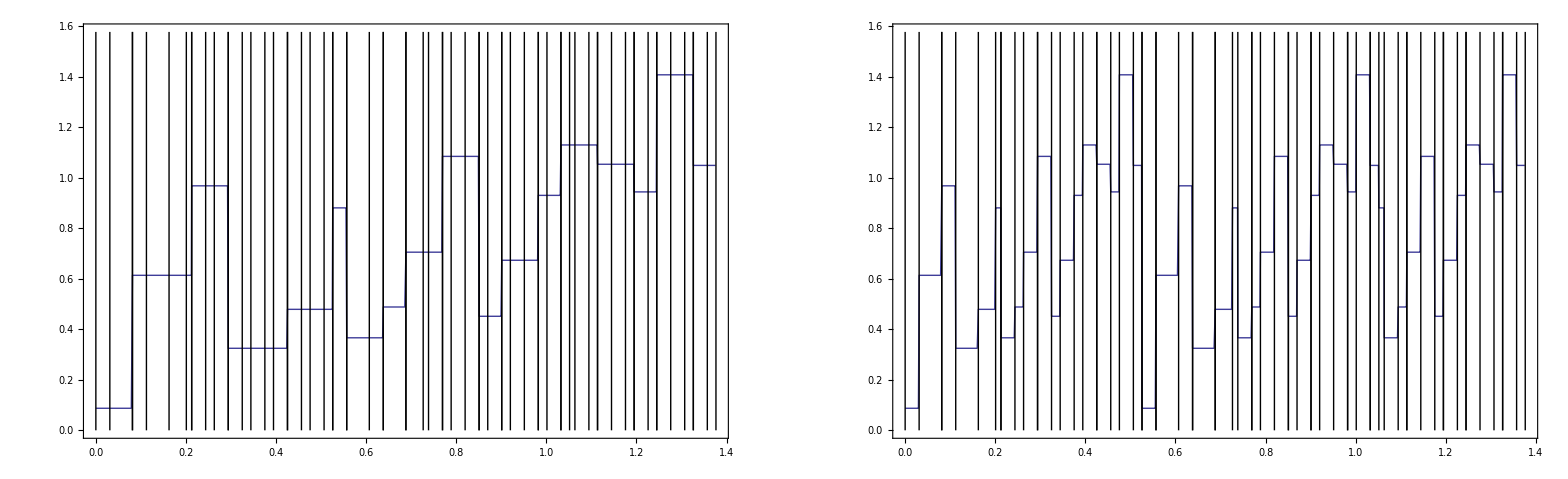

```mathematica
n=20;
a=Table[RandomReal[1],{Length[gridPoint]-1}];
a=a/Sum[a[[i]](gridPoint[[i+1]]-gridPoint[[i]]),{i,Length[a]}]//N
fence=Table[Graphics[Line[{{gridPoint[[i]],0},{gridPoint[[i]],1.1 Max[a]}}]],{i,2,Length[a]}];
fence2=Table[Graphics[{Thick,Line[{{gridPeriodicPoint[[i]],0},{gridPeriodicPoint[[i]],1.1 Max[a]}}]}],{i,Length[gridPeriodicPoint]}];
scale=2;
{plotOfS,plotOfLS,plotOfKS,plotOfKLS}=mapStepFunctionAndPlotResult[];
GraphicsGrid[{{Show[plotOfS,fence,fence2],Show[plotOfLS,fence,fence2]}}]
GraphicsGrid[{{Show[plotOfS,fence,fence2],Show[plotOfKS,fence,fence2]}}]
GraphicsGrid[{{Show[plotOfLS,fence,fence2],Show[plotOfKLS,fence,fence2]}}]
```

```mathematica
cellList=Transpose[{Table[i-1,{i,Length[gridPoint]}],gridPoint}]
L=Table[0,{Length[gridPoint]-1},{Length[gridPoint]-1}];
Do[
Print[i];
interval={gridPoint[[i]]/σ,gridPoint[[i+1]]/σ}/.varSol//N;
cell=cellFind[interval];
Print[interval,"->",cell];
L[[i,cell]]=1;
interval={gridPoint[[i]]/σ+α,gridPoint[[i+1]]/σ+α}/.varSol//N;
cell=cellFind[interval];
Print[interval,"->",cell];
L[[i,cell]]=1;
If[gridPoint[[i]]≥ α/.varSol//N,
interval={gridPoint[[i]]/σ+β,gridPoint[[i+1]]/σ+β}/.varSol//N;
cell=cellFind[interval];
Print[interval,"->",cell]];
  L[[i,cell]]=1,
{i,Length[gridPoint]-1}]
ArrayPlot[L,Mesh->True]
```

{{0,0.},{1,0.0310271},{2,0.0812299},{3,0.112257},{4,0.16246},{5,0.200811},{6,0.212663},{7,0.24369},{8,0.262866},{9,0.293893},{10,0.32492},{11,0.344095},{12,0.375123},{13,0.394298},{14,0.425325},{15,0.456352},{16,0.475528},{17,0.506555},{18,0.525731},{19,0.556758},{20,0.606961},{21,0.637988},{22,0.688191},{23,0.726543},{24,0.738394},{25,0.769421},{26,0.788597},{27,0.819624},{28,0.850651},{29,0.869827},{30,0.900854},{31,0.920029},{32,0.951057},{33,0.982084},{34,1.00126},{35,1.03229},{36,1.05146},{37,1.06331},{38,1.09434},{39,1.11352},{40,1.14454},{41,1.17557},{42,1.19475},{43,1.22577},{44,1.24495},{45,1.27598},{46,1.307},{47,1.32618},{48,1.35721},{49,1.37638}}

1

{0.,0.0118513}->1

{0.525731,0.537582}->19

2

{0.0118513,0.0310271}->1

{0.537582,0.556758}->19

3

{0.0310271,0.0428784}->2

{0.556758,0.568609}->20

4

{0.0428784,0.0620541}->2

{0.568609,0.587785}->20

5

{0.0620541,0.0767031}->2

{0.587785,0.602434}->20

6

{0.0767031,0.0812299}->2

{0.602434,0.606961}->20

7

{0.0812299,0.0930812}->3

{0.606961,0.618812}->21

8

{0.0930812,0.100406}->3

{0.618812,0.626137}->21

9

{0.100406,0.112257}->3

{0.626137,0.637988}->21

10

{0.112257,0.124108}->4

{0.637988,0.649839}->22

11

{0.124108,0.131433}->4

{0.649839,0.657164}->22

12

{0.131433,0.143284}->4

{0.657164,0.669015}->22

13

{0.143284,0.150609}->4

{0.669015,0.67634}->22

14

{0.150609,0.16246}->4

{0.67634,0.688191}->22

15

{0.16246,0.174311}->5

{0.688191,0.700042}->23

16

{0.174311,0.181636}->5

{0.700042,0.707367}->23

17

{0.181636,0.193487}->5

{0.707367,0.719218}->23

18

{0.193487,0.200811}->5

{0.719218,0.726543}->23

19

{0.200811,0.212663}->6

{0.726543,0.738394}->24

{1.05146,1.06331}->37

20

{0.212663,0.231838}->7

{0.738394,0.75757}->25

{1.06331,1.08249}->38

21

{0.231838,0.24369}->7

{0.75757,0.769421}->25

{1.08249,1.09434}->38

22

{0.24369,0.262866}->8

{0.769421,0.788597}->26

{1.09434,1.11352}->39

23

{0.262866,0.277515}->9

{0.788597,0.803246}->27

{1.11352,1.12817}->40

24

{0.277515,0.282041}->9

{0.803246,0.807772}->27

{1.12817,1.13269}->40

25

{0.282041,0.293893}->9

{0.807772,0.819624}->27

{1.13269,1.14454}->40

26

{0.293893,0.301217}->10

{0.819624,0.826948}->28

{1.14454,1.15187}->41

27

{0.301217,0.313068}->10

{0.826948,0.8388}->28

{1.15187,1.16372}->41

28

{0.313068,0.32492}->10

{0.8388,0.850651}->28

{1.16372,1.17557}->41

29

{0.32492,0.332244}->11

{0.850651,0.857975}->29

{1.17557,1.1829}->42

30

{0.332244,0.344095}->11

{0.857975,0.869827}->29

{1.1829,1.19475}->42

31

{0.344095,0.35142}->12

{0.869827,0.877151}->30

{1.19475,1.20207}->43

32

{0.35142,0.363271}->12

{0.877151,0.889002}->30

{1.20207,1.21392}->43

33

{0.363271,0.375123}->12

{0.889002,0.900854}->30

{1.21392,1.22577}->43

34

{0.375123,0.382447}->13

{0.900854,0.908178}->31

{1.22577,1.2331}->44

35

{0.382447,0.394298}->13

{0.908178,0.920029}->31

{1.2331,1.24495}->44

36

{0.394298,0.401623}->14

{0.920029,0.927354}->32

{1.24495,1.25227}->45

37

{0.401623,0.40615}->14

{0.927354,0.931881}->32

{1.25227,1.2568}->45

38

{0.40615,0.418001}->14

{0.931881,0.943732}->32

{1.2568,1.26865}->45

39

{0.418001,0.425325}->14

{0.943732,0.951057}->32

{1.26865,1.27598}->45

40

{0.425325,0.437177}->15

{0.951057,0.962908}->33

{1.27598,1.28783}->46

41

{0.437177,0.449028}->15

{0.962908,0.974759}->33

{1.28783,1.29968}->46

42

{0.449028,0.456352}->15

{0.974759,0.982084}->33

{1.29968,1.307}->46

43

{0.456352,0.468204}->16

{0.982084,0.993935}->34

{1.307,1.31885}->47

44

{0.468204,0.475528}->16

{0.993935,1.00126}->34

{1.31885,1.32618}->47

45

{0.475528,0.48738}->17

{1.00126,1.01311}->35

{1.32618,1.33803}->48

46

{0.48738,0.499231}->17

{1.01311,1.02496}->35

{1.33803,1.34988}->48

47

{0.499231,0.506555}->17

{1.02496,1.03229}->35

{1.34988,1.35721}->48

48

{0.506555,0.518407}->18

{1.03229,1.04414}->36

{1.35721,1.36906}->49

49

{0.518407,0.525731}->18

{1.04414,1.05146}->36

{1.36906,1.37638}->49

-Graphics-

```mathematica
AdjacencyGraph[L,GraphStyle->"VintageDiagram"]
```

-Graphics-

```mathematica
19-7
```

12

```mathematica
K=Join[IdentityMatrix[Length[gridPeriodicPoint]-1],IdentityMatrix[Length[gridPeriodicPoint]-1],Take[IdentityMatrix[Length[gridPeriodicPoint]-1],-13]];
```

```mathematica
K//TraditionalForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Because 𝒦 is rectangular we cannot find a spectral decomposition. However the singular value decomposition is always possible.

```mathematica
{UK,WK,VK}=SingularValueDecomposition[K];
UK//TraditionalForm
Transpose[UK].UK==IdentityMatrix[Length[UK]]
WK//TraditionalForm
VK//TraditionalForm
Transpose[VK].VK==IdentityMatrix[Length[VK]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

True

(√3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | √3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

True

```mathematica
K==UK.WK.Transpose[VK]
```

True

```mathematica
SingularValueList[K]
```

{√3,√3,√3,√3,√3,√3,√3,√3,√3,√3,√3,√3,√3,√2,√2,√2,√2,√2}

```mathematica
Transpose[K].K//TraditionalForm
Eigensystem[Transpose[K].K]
%[[2]]//TraditionalForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3)

{{3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

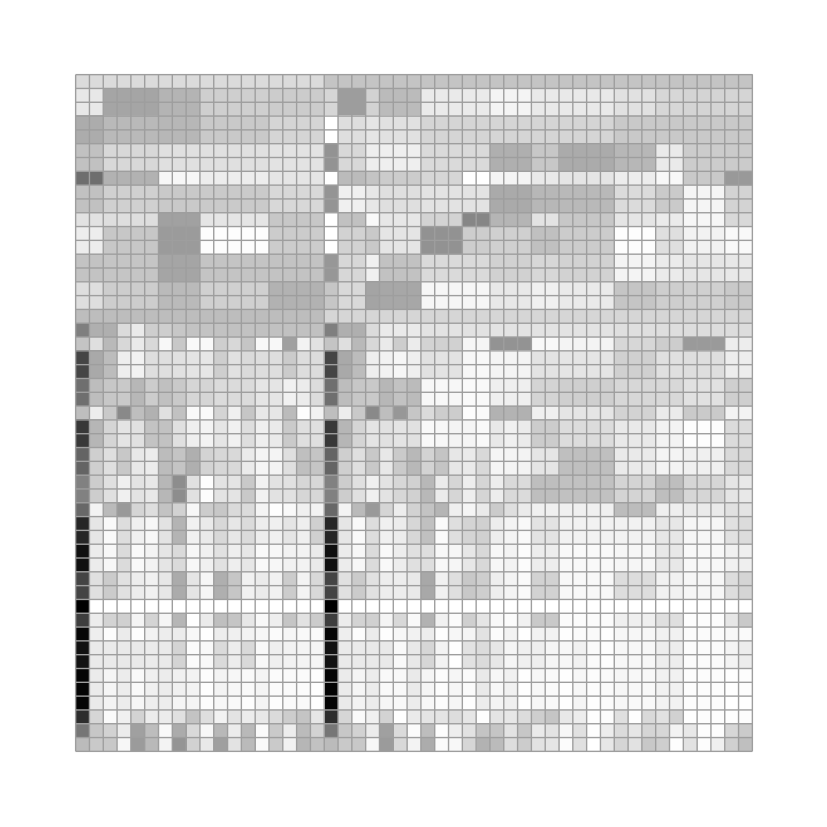

{1.,-0.190983+0.330792 ⅈ,-0.190983-0.330792 ⅈ,0.381966,0.381966,-0.190983+0.330792 ⅈ,-0.190983-0.330792 ⅈ,0.381966,-0.190983+0.330792 ⅈ,-0.190983-0.330792 ⅈ,0.381966,0.381966,0.381966,-0.190983+0.330792 ⅈ,-0.190983-0.330792 ⅈ,-0.190983+0.330792 ⅈ,-0.190983-0.330792 ⅈ,0.145898,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
L=L/σ;
{λ,ρ}=Eigensystem[L/.σSol//N]//Chop;
ArrayPlot[ρ,Mesh->True]
λ
```

```mathematica
{UL,WL,VL}=SingularValueDecomposition[L/.σSol//N]//Chop;
```

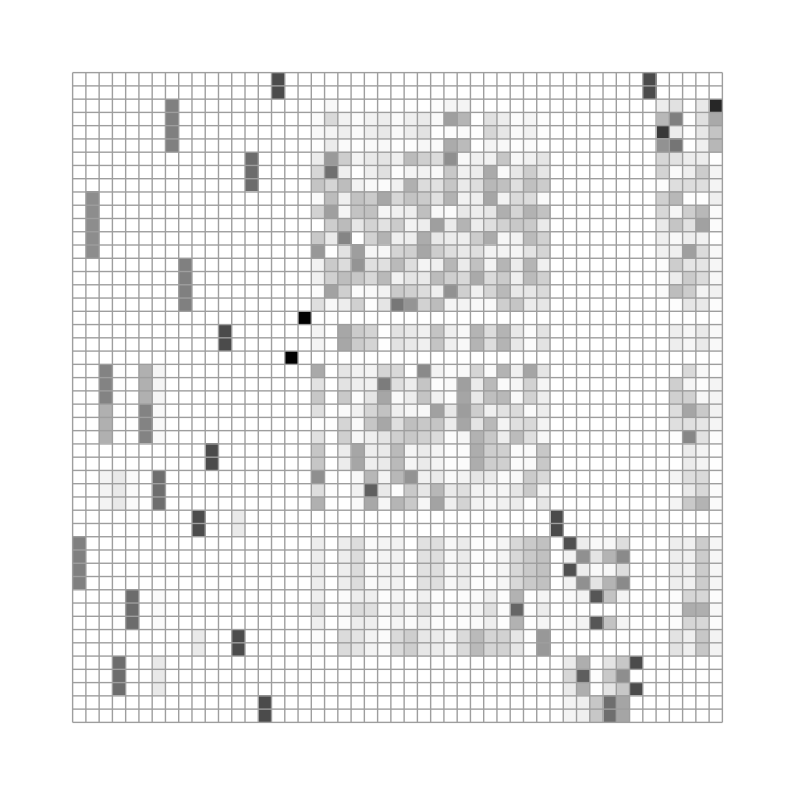

True

```mathematica
ArrayPlot[UL,Mesh->True]
Chop[UL.Transpose[UL]]==IdentityMatrix[Length[UL]]
```

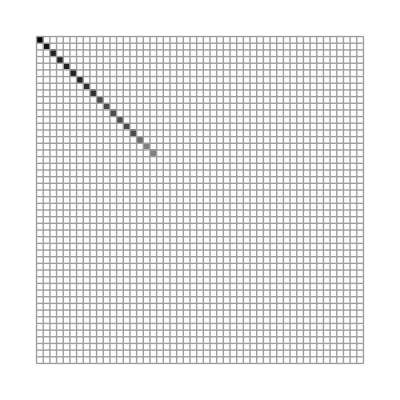

```mathematica
ArrayPlot[WL,Mesh->True]
```

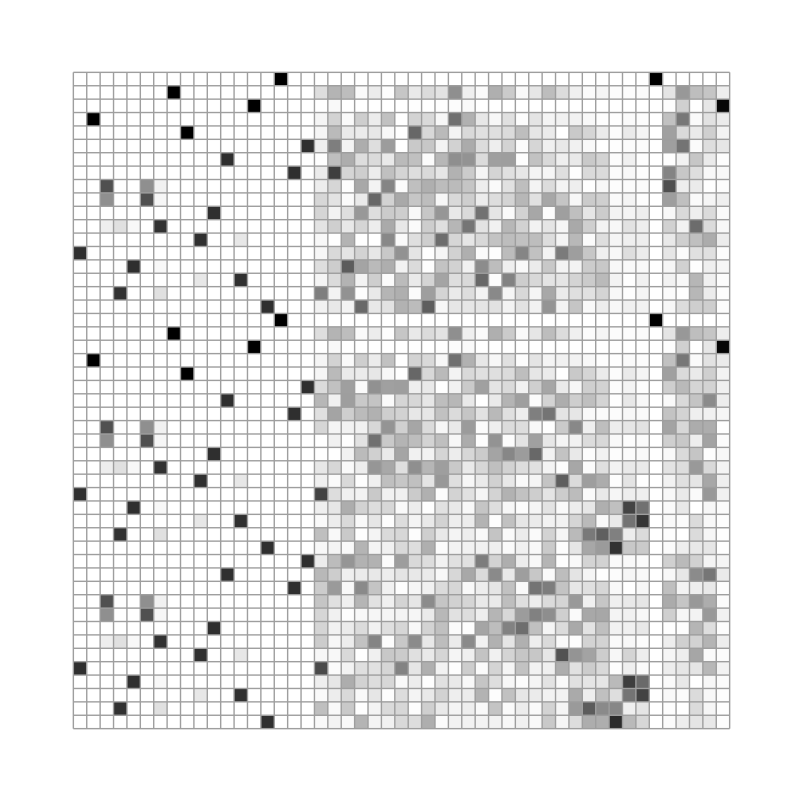

True

```mathematica
ArrayPlot[VL,Mesh->True]
Chop[VL.Transpose[VL]]==IdentityMatrix[Length[UL]]
```

```mathematica
(L/.σSol//N)==UL.WL.Transpose[VL]
```

False

```mathematica
SingularValueList[L]
```

{2 √3 √(1/(σ Conjugate[σ])),√10 √(1/(σ Conjugate[σ])),3 √(1/(σ Conjugate[σ])),3 √(1/(σ Conjugate[σ])),3 √(1/(σ Conjugate[σ])),3 √(1/(σ Conjugate[σ])),3 √(1/(σ Conjugate[σ])),2 √2 √(1/(σ Conjugate[σ])),2 √2 √(1/(σ Conjugate[σ])),√6 √(1/(σ Conjugate[σ])),√6 √(1/(σ Conjugate[σ])),√6 √(1/(σ Conjugate[σ])),√6 √(1/(σ Conjugate[σ])),√6 √(1/(σ Conjugate[σ])),√6 √(1/(σ Conjugate[σ])),2 √(1/(σ Conjugate[σ])),√3 √(1/(σ Conjugate[σ])),√3 √(1/(σ Conjugate[σ]))}

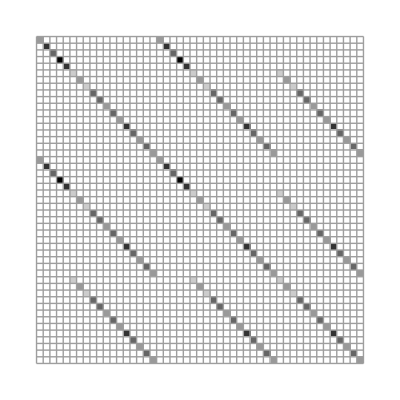

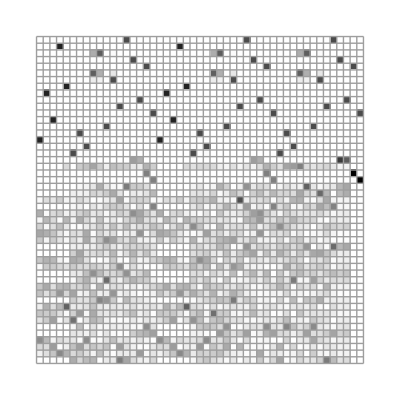

```mathematica
ArrayPlot[Chop[Transpose[(L/.σSol//N)].(L/.σSol//N)],Mesh-> True]
Eigensystem[Chop[Transpose[(L/.σSol//N)].(L/.σSol//N)]]//Chop;
ArrayPlot[%[[2]],Mesh-> True]
```

#### Period 3 periodic point n=49 partition - Spectral decomposition

```mathematica
CharacteristicPolynomial[L,z]//N
Factor[%]
```

-1. z^49-(1. z^31)/σ^18+(4. z^32)/σ^17-(4. z^33)/σ^16+(6. z^34)/σ^15-(20. z^35)/σ^14+(20. z^36)/σ^13-(15. z^37)/σ^12+(40. z^38)/σ^11-(40. z^39)/σ^10+(20. z^40)/σ^9-(40. z^41)/σ^8+(40. z^42)/σ^7-(15. z^43)/σ^6+(20. z^44)/σ^5-(20. z^45)/σ^4+(6. z^46)/σ^3-(4. z^47)/σ^2+(4. z^48)/σ

-1/σ^181. z^31 (1.-4. z σ+4. z^2 σ^2-6. z^3 σ^3+20. z^4 σ^4-20. z^5 σ^5+15. z^6 σ^6-40. z^7 σ^7+40. z^8 σ^8-20. z^9 σ^9+40. z^10 σ^10-40. z^11 σ^11+15. z^12 σ^12-20. z^13 σ^13+20. z^14 σ^14-6. z^15 σ^15+4. z^16 σ^16-4. z^17 σ^17+1. z^18 σ^18)

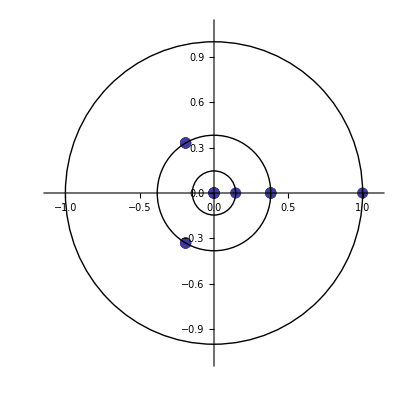

```mathematica
Show[ListPlot[{Re[#],Im[#]}&/@λ//N,AspectRatio->Automatic,PlotRange->{{-1.1,1.1},{-1.1,1.1}},ImageSize->Scaled[0.5],PlotStyle->PointSize[0.02]],circle1,circle2,circle3]/.σSol//N
```

```mathematica
Table[{i,λ[[i]],Abs[λ[[i]]]},{i,Length[λ]}]//Chop
```

{{1,1.,1.},{2,-0.190983+0.330792 ⅈ,0.381966},{3,-0.190983-0.330792 ⅈ,0.381966},{4,0.381966,0.381966},{5,0.381966,0.381966},{6,-0.190983+0.330792 ⅈ,0.381966},{7,-0.190983-0.330792 ⅈ,0.381966},{8,0.381966,0.381966},{9,-0.190983+0.330792 ⅈ,0.381966},{10,-0.190983-0.330792 ⅈ,0.381966},{11,0.381966,0.381966},{12,0.381966,0.381966},{13,0.381966,0.381966},{14,-0.190983+0.330792 ⅈ,0.381966},{15,-0.190983-0.330792 ⅈ,0.381966},{16,-0.190983+0.330792 ⅈ,0.381966},{17,-0.190983-0.330792 ⅈ,0.381966},{18,0.145898,0.145898},{19,0,0},{20,0,0},{21,0,0},{22,0,0},{23,0,0},{24,0,0},{25,0,0},{26,0,0},{27,0,0},{28,0,0},{29,0,0},{30,0,0},{31,0,0},{32,0,0},{33,0,0},{34,0,0},{35,0,0},{36,0,0},{37,0,0},{38,0,0},{39,0,0},{40,0,0},{41,0,0},{42,0,0},{43,0,0},{44,0,0},{45,0,0},{46,0,0},{47,0,0},{48,0,0},{49,0,0}}

1

1.

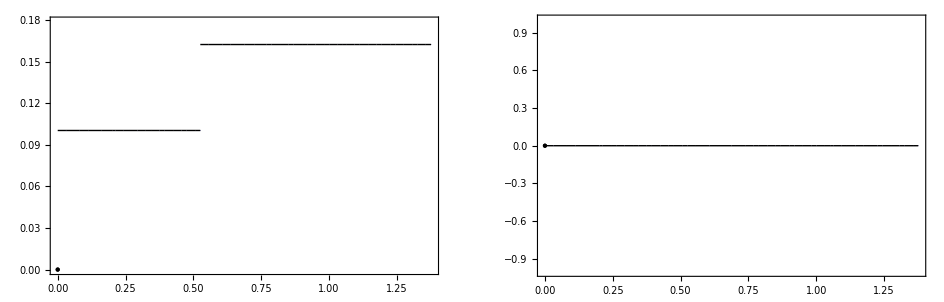

```mathematica
l=1
λ[[l]]
plotEigenstate[ρ[[l]],False]
```

2

-0.190983+0.330792 ⅈ

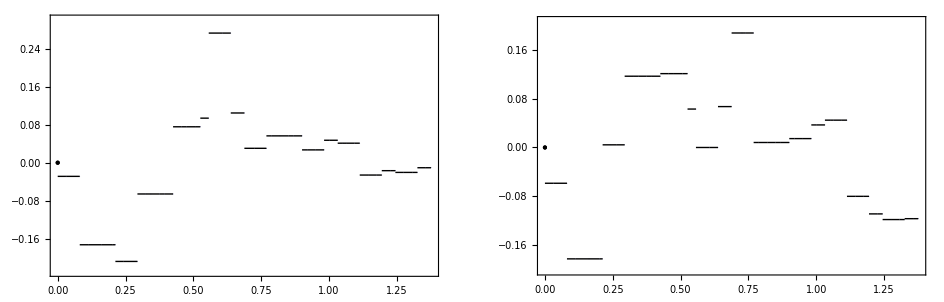

3

-0.190983-0.330792 ⅈ

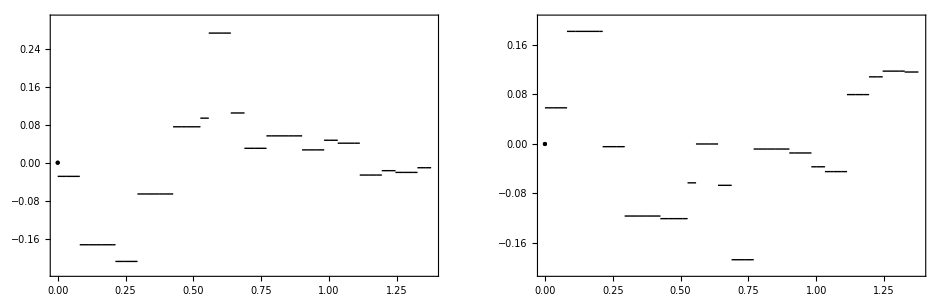

4

0.381966

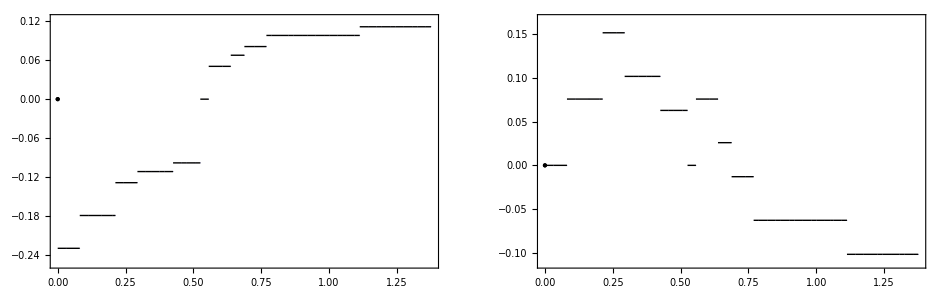

11

0.381966

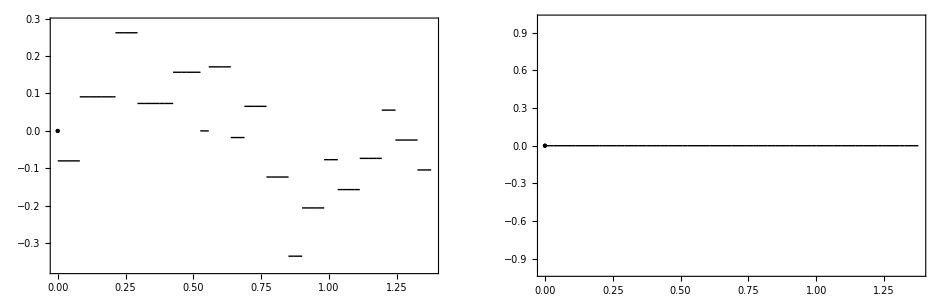

14

-0.190983+0.330792 ⅈ

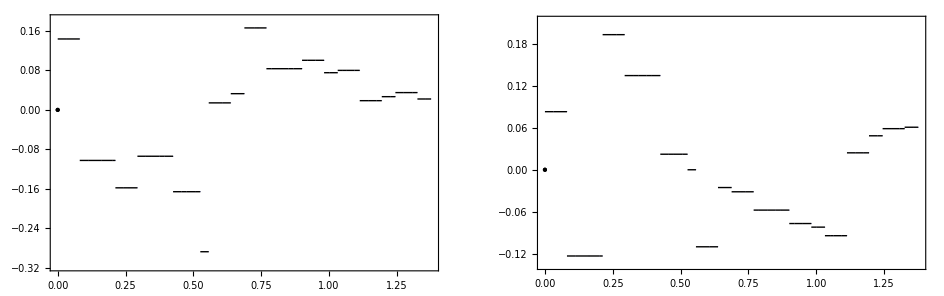

15

-0.190983-0.330792 ⅈ

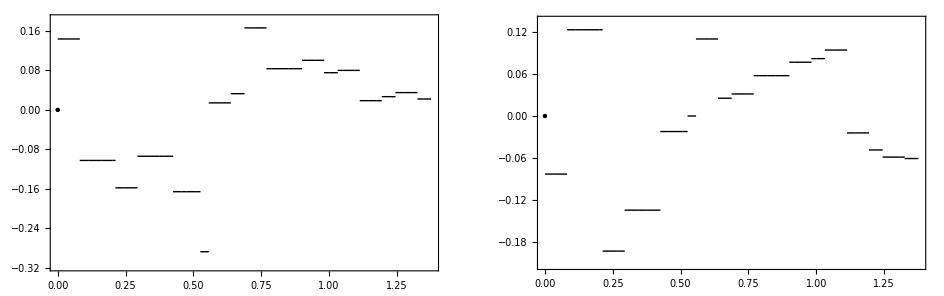

```mathematica
l=2
λ[[l]]
plotEigenstate[ρ[[l]],False]
l=3
λ[[l]]
plotEigenstate[ρ[[l]],False]
l=4
λ[[l]]
plotEigenstate[ρ[[l]],False]
l=11
λ[[l]]
plotEigenstate[ρ[[l]],False]
l=14
λ[[l]]
plotEigenstate[ρ[[l]],False]
l=15
λ[[l]]
plotEigenstate[ρ[[l]],False]
```

5

0.381966

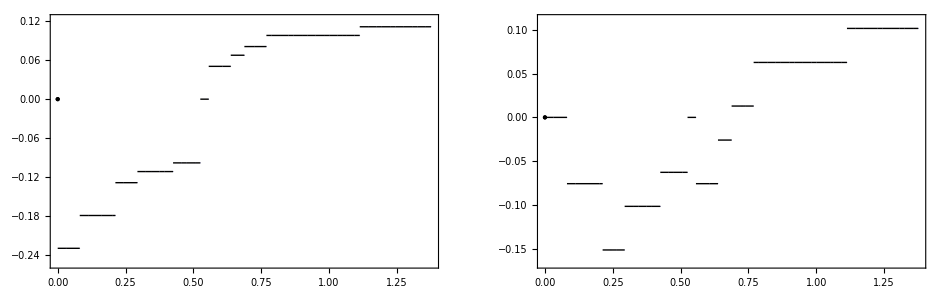

7

-0.190983-0.330792 ⅈ

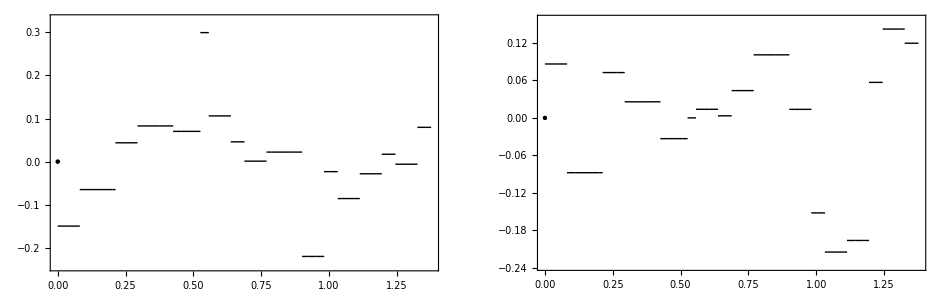

9

-0.190983+0.330792 ⅈ

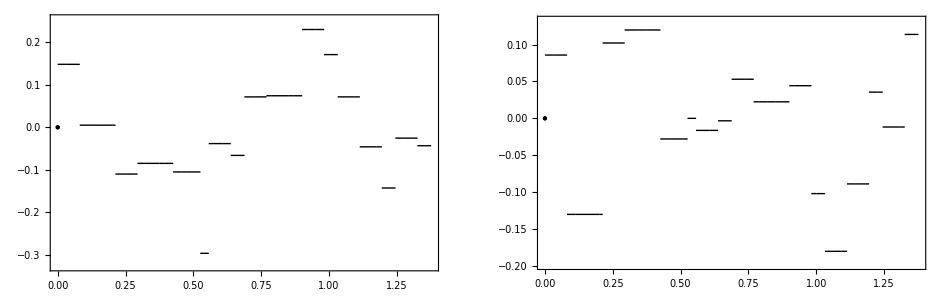

12

0.381966

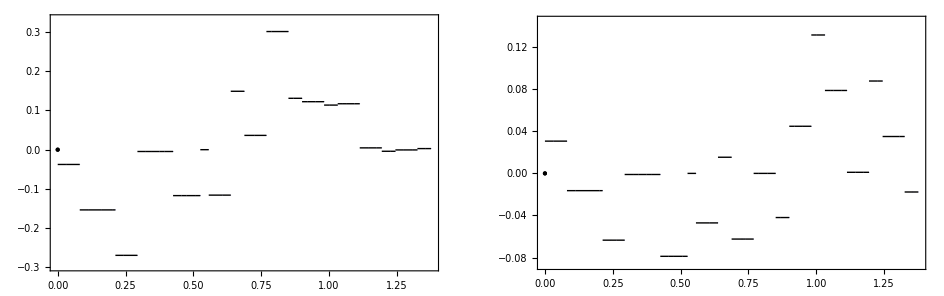

16

-0.190983+0.330792 ⅈ

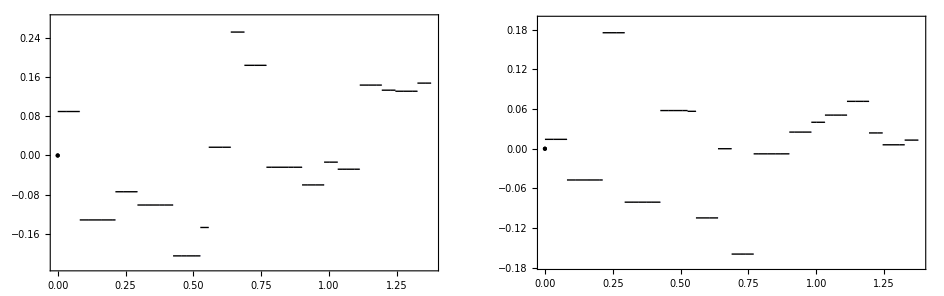

```mathematica
l=5
λ[[l]]
plotEigenstate[ρ[[l]],False]
l=7
λ[[l]]
plotEigenstate[ρ[[l]],False]
l=9
λ[[l]]
plotEigenstate[ρ[[l]],False]
l=12
λ[[l]]
plotEigenstate[ρ[[l]],False]
l=16
λ[[l]]
plotEigenstate[ρ[[l]],False]
```

18

0.145898

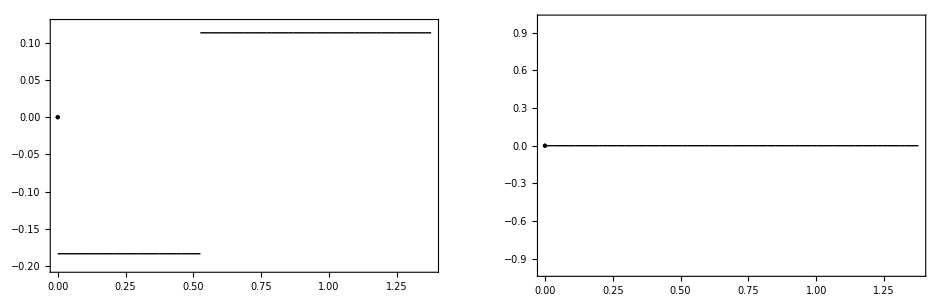

```mathematica
l=18
λ[[l]]
plotEigenstate[ρ[[l]],False]
```

19

0

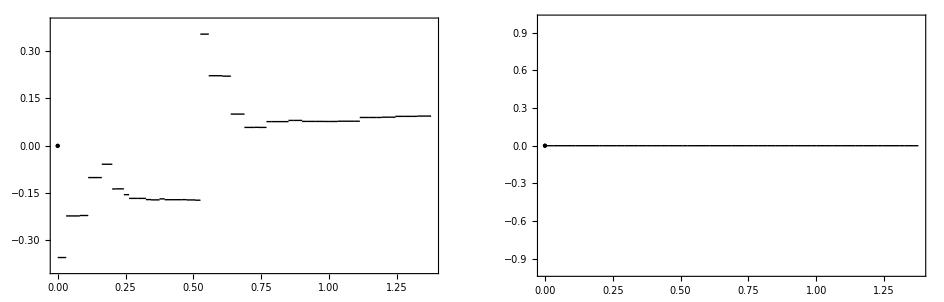

20

0

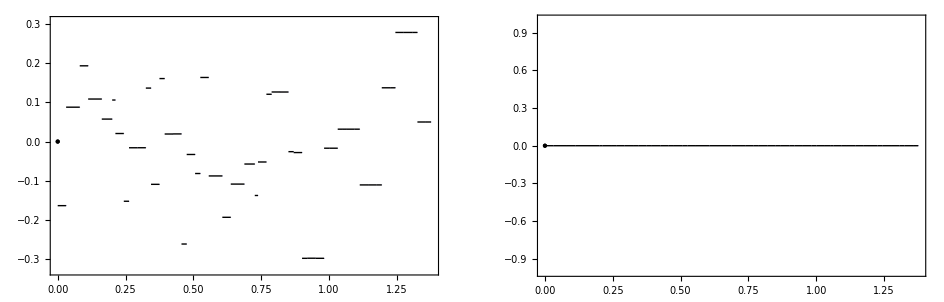

21

0

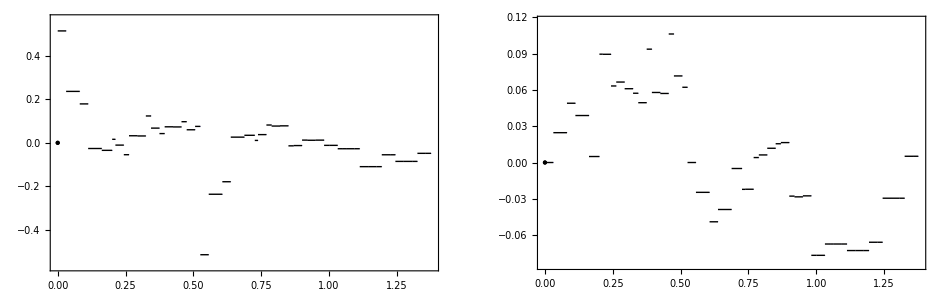

23

0

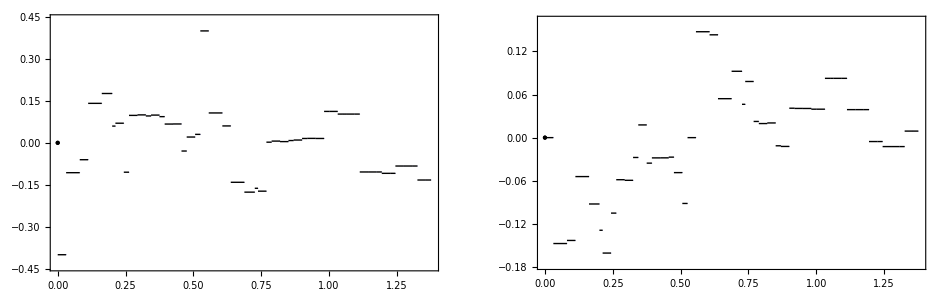

25

0

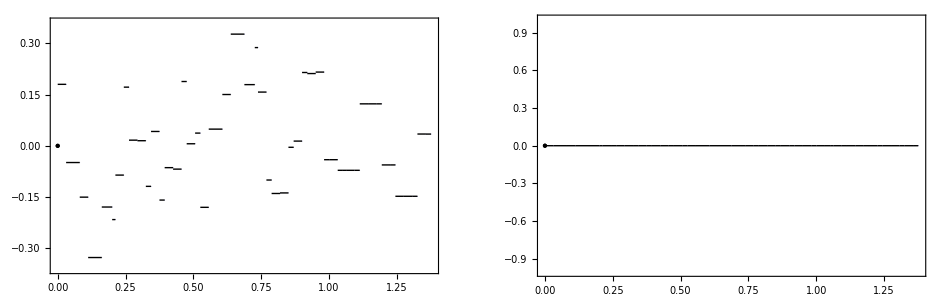

```mathematica
l=19
λ[[l]]
plotEigenstate[ρ[[l]],False]
l=20
λ[[l]]
plotEigenstate[ρ[[l]],False]
l=21
λ[[l]]
plotEigenstate[ρ[[l]],False]
l=23
λ[[l]]
plotEigenstate[ρ[[l]],False]
l=25
λ[[l]]
plotEigenstate[ρ[[l]],False]
```

#### Period 3 periodic point n=49 partition - Dual Space

```mathematica
Clear[c,χ]
χ = Table[c[i,j],{i,Length[L]},{j,Length[L]}];
χSol=Solve[Table[χ[[i]].ρ[[j]]==If[i==j,1,0],{i,Length[L]},{j,Length[L]}]//Flatten,χ//Flatten]//Chop;
```

1

1.

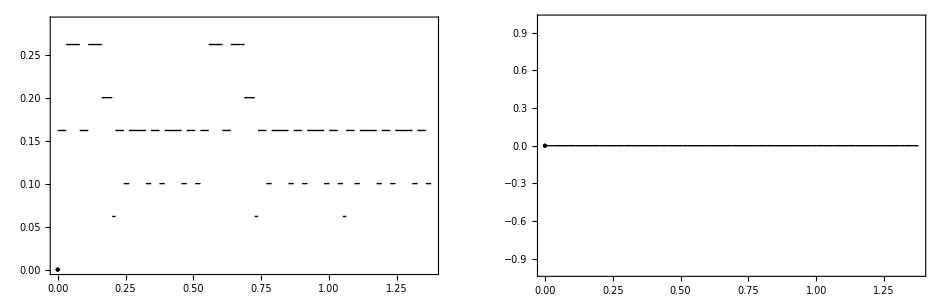

```mathematica
l=1
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],False]
```

2

-0.190983+0.330792 ⅈ

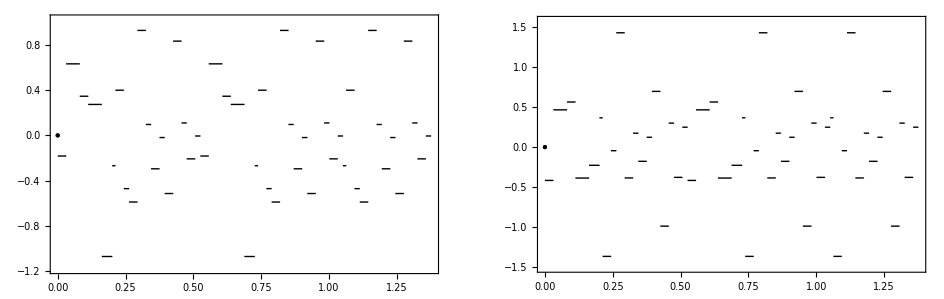

3

-0.190983-0.330792 ⅈ

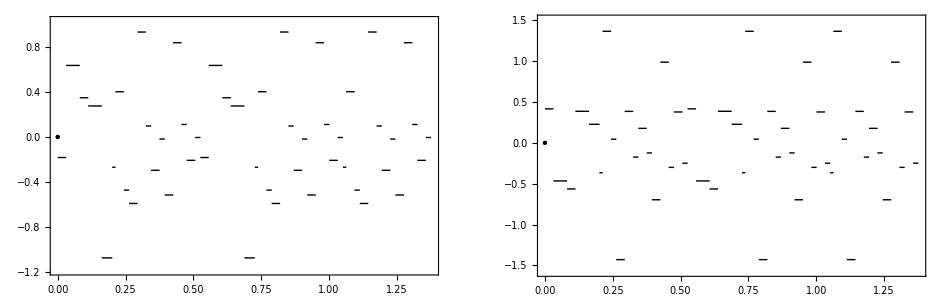

4

0.381966

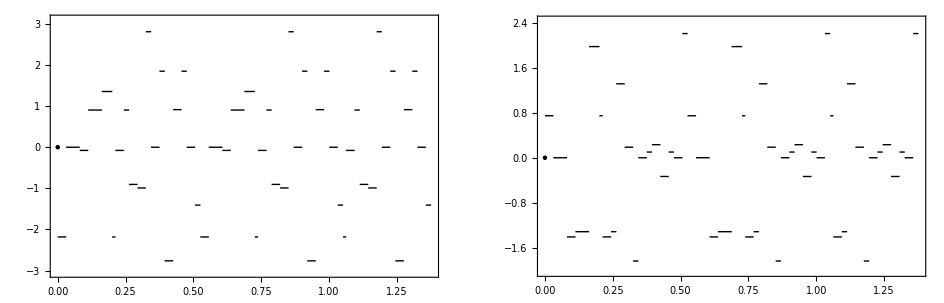

11

0.381966

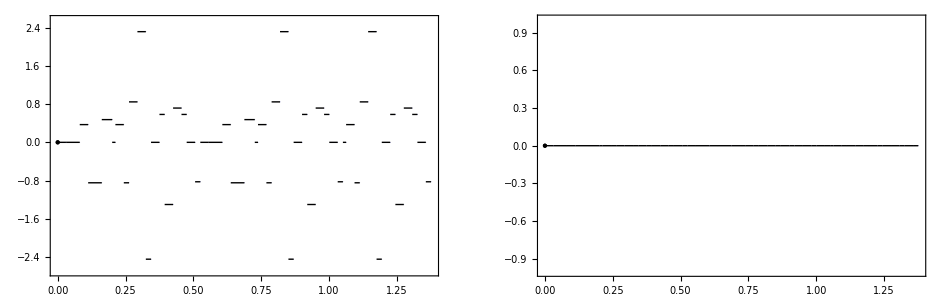

14

-0.190983+0.330792 ⅈ

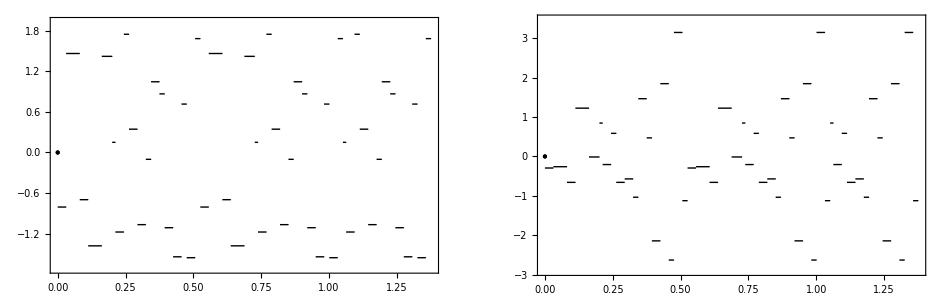

15

-0.190983-0.330792 ⅈ

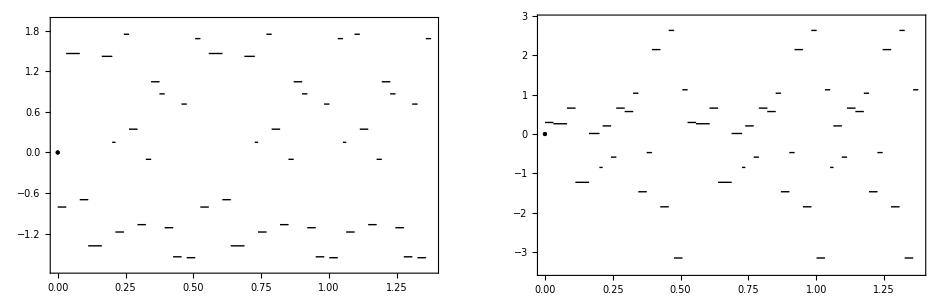

```mathematica
l=2
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],False]
l=3
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],False]
l=4
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],False]
l=11
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],False]
l=14
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],False]
l=15
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],False]
```

5

0.381966

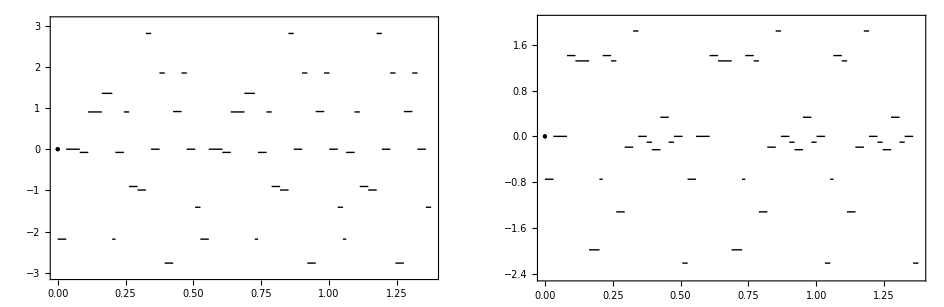

7

-0.190983-0.330792 ⅈ

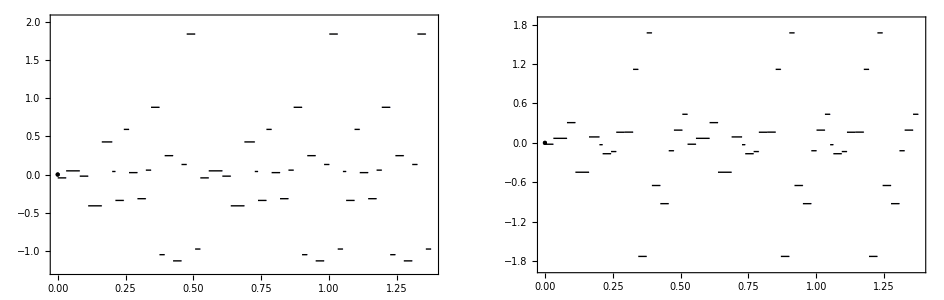

9

-0.190983+0.330792 ⅈ

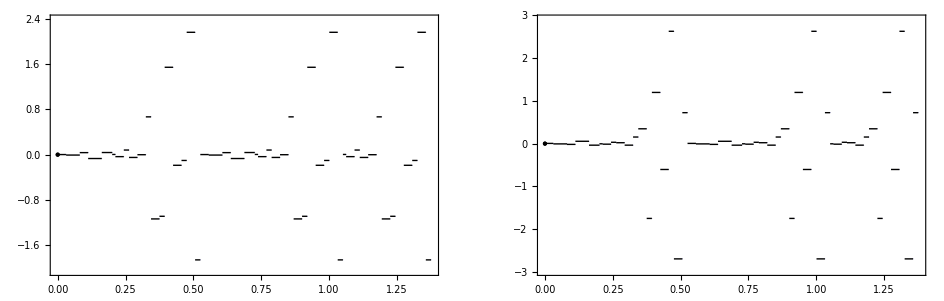

12

0.381966

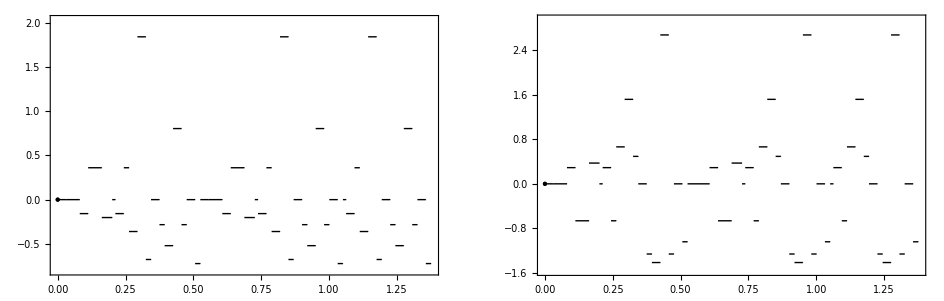

16

-0.190983+0.330792 ⅈ

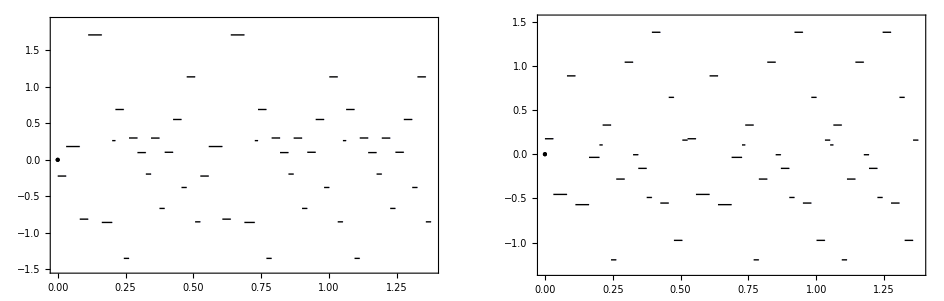

```mathematica
l=5
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],False]
l=7
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],False]
l=9
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],False]
l=12
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],False]
l=16
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],False]
```

18

0.145898

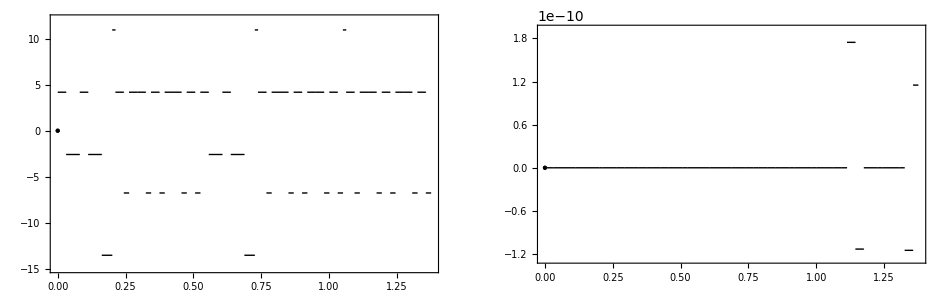

```mathematica
l=18
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]],False]
```

19

0

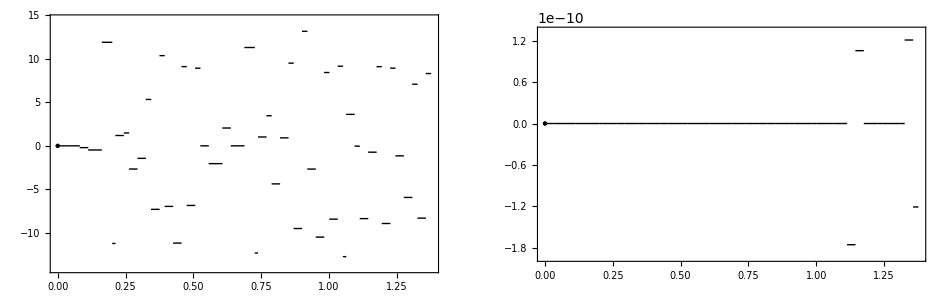

20

0

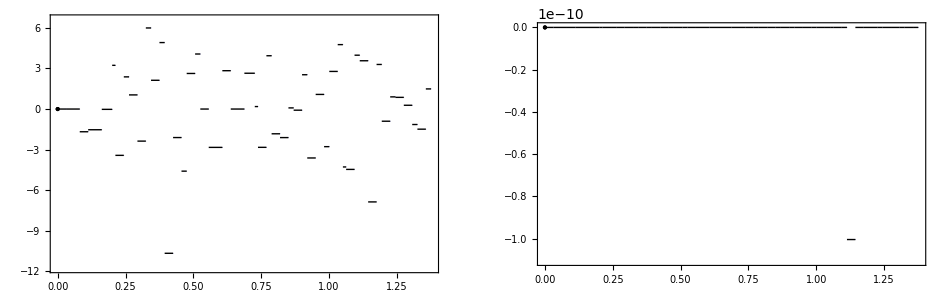

21

0

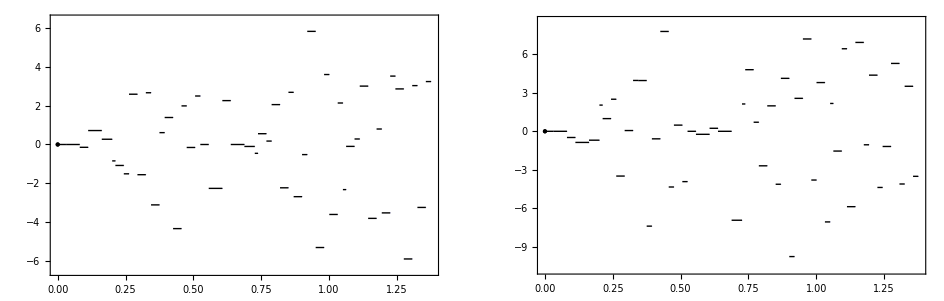

23

0

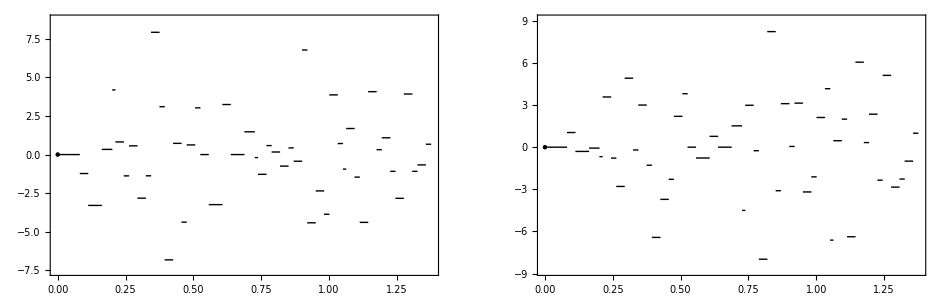

25

0

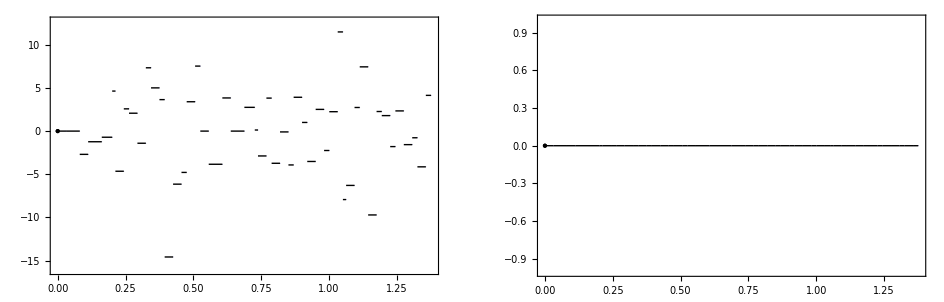

```mathematica
l=19
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]]//Chop,False]
l=20
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]]//Chop,False]
l=21
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]]//Chop,False]
l=23
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]]//Chop,False]
l=25
λ[[l]]
plotEigenstate[χ[[l]]/.χSol[[1]]//Chop,False]
```

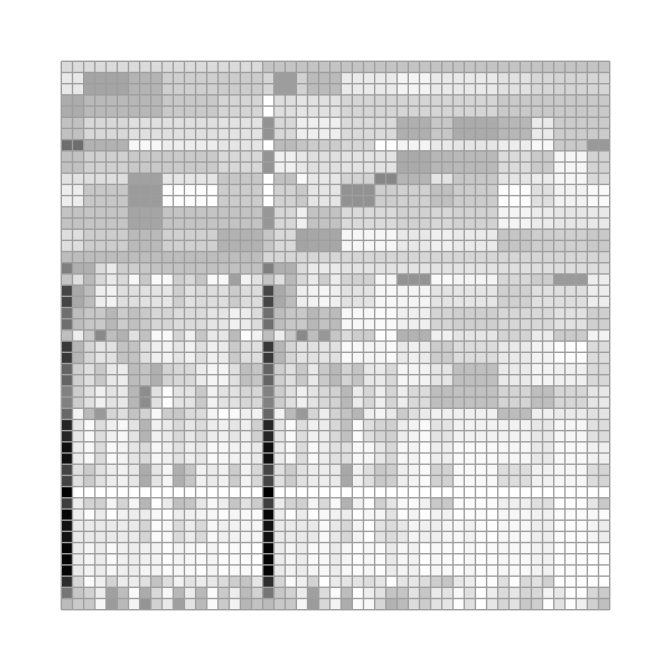

0

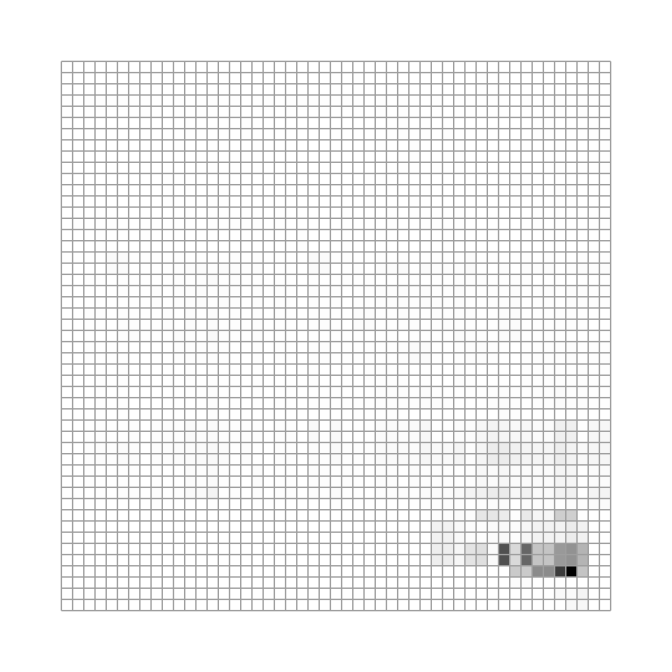

9.97339×10^28-4.6728×10^41 ⅈ

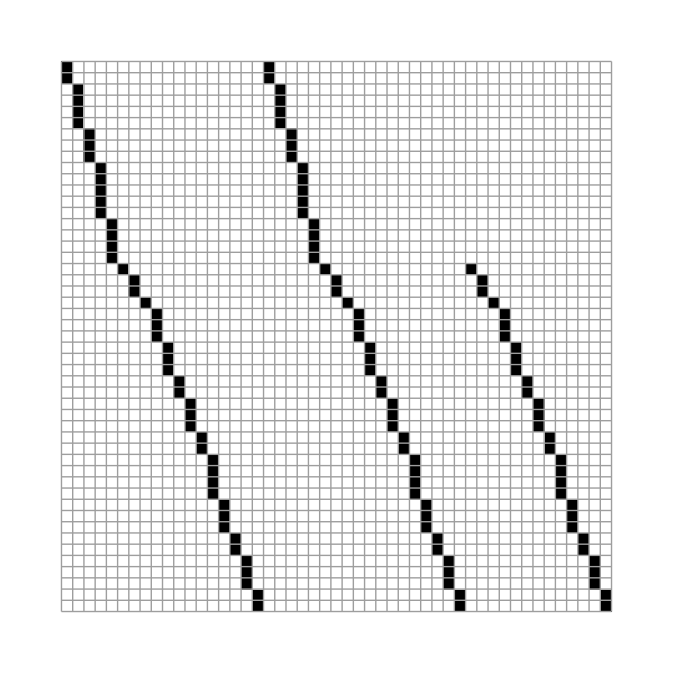

False

```mathematica
ArrayPlot[ρ//Chop,Mesh-> True]
Det[ρ]//Chop
ArrayPlot[χ/.χSol[[1]]//Chop,Mesh-> True]
Det[χ/.χSol[[1]]//Chop]//Chop
ArrayPlot[Transpose[ρ].DiagonalMatrix[λ].χ/.χSol[[1]]//Chop,Mesh-> True]
(L/.σSol//N)==Chop[Transpose[ρ].DiagonalMatrix[λ].χ/.χSol[[1]]]
```